# Woods-Saxon Potential

## Micah Buuck

6/20/13

## Constants and Initial Conditions

Originally I tried to make use of Mathematica's built-in unit handling, but I couldn't figure out how to make that work with plotting, so I gave up. I left the code for it in, but commented it out.

```mathematica
(*<<Units`
Needs["PhysicalConstants`"]*)
Needs["PlotLegends`"]
```

```mathematica
m=938.272046(*Mega ElectronVolt*);
ℏc=197.32697178(*Mega ElectronVolt*Femto Meter*);
R=(2/3*.535)^(-1/2) (*Femto Meter*);
V0=-41.5-8.3 I(*Mega ElectronVolt*);
a=.54(*Femto Meter*);
V[r_]:=V0/(1+E^((r-R)/a));
```

### Plot for potential

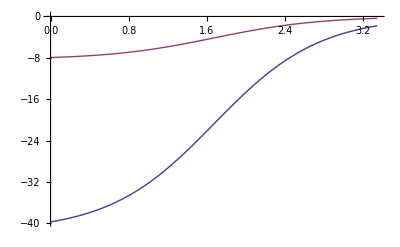

```mathematica
Plot[{Re[V[r]],Im[V[r]]},{r,0,2*R}]
```

## Solve the Schrödinger Equation

First I solve the Schrödinger equation for the radial wavefunction with an arbitrary constant for the initial condition for u'(0). My goal is to show that the resulting phase shift we get from this in independent of the choice of u'(0).

```mathematica
s[L_,k_,b_]:=NDSolve[{u''[r]+(k^2-2*m/(ℏc)^2*V[r]-L*(L+1)/r^2)*u[r]==0,u[(1000*k)^(-1)]==0,u'[(1000*k)^(-1)]==b},u,{r,(1000*k)^(-1),5*R}]
```

```mathematica
u[L_,k_,r_,b_]:=u[r]/.s[L,k,b][[1]]
```

```mathematica
β[L_,k_,b_]:=5*R/Evaluate[u[L,k,5*R,b]]*(D[u[L,k,r,b],r]/.r->(5*R))-1
tanδ[L_,k_,b_]:=N[(k*5*R*Derivative[0,1][SphericalBesselJ][L,k*5*R]-β[L,k,b]*SphericalBesselJ[L,k*5*R])/(k*5*R*Derivative[0,1][SphericalBesselY][L,k*5*R]-β[L,k,b]*SphericalBesselY[L,k*5*R])]
```

```mathematica
(*Plot[Re[tanδ[0,1,b]],{b,0.01,10}]*)
```

```mathematica
(*Plot[Im[tanδ[0,1,b]],{b,0.01,10}]*)
```

As we can see from this plot of tanδ vs. u'(0), the phase shift appears to be independent of our choice of u'(0) up to about 0.01% error.

## Reformulate tanδ for specific choice of u'(0)

These are the same equations as above, but now we have chosen u'(0)=8 (an arbitrary choice).

```mathematica
s[L_,k_]:=NDSolve[{u''[r]+(k^2-2*m/(ℏc)^2*V[r]-L*(L+1)/r^2)*u[r]==0,u[(1000*k)^(-1)]==0,u'[(1000*k)^(-1)]==8},u,{r,(1000*k)^(-1),5*R},MaxSteps->20000]
```

```mathematica
u[L_,k_,r_]:=u[r]/.s[L,k][[1]]
```

```mathematica
β[L_,k_]:=5*R/Evaluate[u[L,k,5*R]]*(D[u[L,k,r],r]/.r->(5*R))-1
tanδ[L_,k_]:=N[(k*5*R*Derivative[0,1][SphericalBesselJ][L,k*5*R]-β[L,k]*SphericalBesselJ[L,k*5*R])/(k*5*R*Derivative[0,1][SphericalBesselY][L,k*5*R]-β[L,k]*SphericalBesselY[L,k*5*R])]
```

```mathematica
Table[Abs[tanδ[L,5]]/Abs[tanδ[0,5]],{L,0,20}]
```

{1.,0.984183,0.948468,0.896954,0.830717,0.751538,0.662308,0.567258,0.471681,0.381014,0.299674,0.230279,0.173558,0.128787,0.0944055,0.0685565,0.0494291,0.035445,0.0253117,0.0180171,0.0127933}

For k=1, tanδ becomes negligible after about L=5.

Below is an automated limit calculator for the phase shift series. The tolerance for the maximum allowed relative magnitude of the last term in the series to the initial term in the series is an adjustable parameter, with a default value of 10^-4.

```mathematica
Lim[k_,tol_:10^-4]:=(err=1;L=0;While[err>tol,err=Abs[tanδ[L,k]]/Abs[tanδ[0,k]];L++];Return[L])
```

```mathematica
Liminterp=Interpolation[Table[{k,Lim[k]},{k,.1,10,.1}]];
```

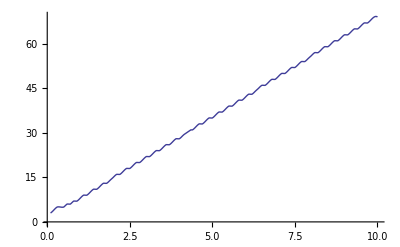

```mathematica
Plot[Liminterp[k],{k,.1,10}]
```

Plugging this phase shift into the equations for the scattering amplitude is:

```mathematica
f[k_,θ_]:=1/k*Sum[(2*L+1)*tanδ[L,k]/(1-I*tanδ[L,k])*LegendreP[L,Cos[θ]],{L,0,Ceiling[Liminterp[k]]}]
```

Here is a table of some values of dσ/dΩ as a function of θ.

```mathematica
Clear[dσdΩ]
```

```mathematica
dσdΩ[En_,points_:10]:=Table[{θ,Abs[f[Sqrt[En^2+2*m*En]/ℏc,θ]]^2},{θ,0,Pi,N[1/points]}]
```

```mathematica
dσdΩ[100]
```

{{0.,35.065},{0.1,31.6488},{0.2,23.3439},{0.3,14.1876},{0.4,7.17729},{0.5,3.04711},{0.6,1.09319},{0.7,0.340149},{0.8,0.104358},{0.9,0.0434705},{1.,0.0269933},{1.1,0.0182259},{1.2,0.0111292},{1.3,0.00595555},{1.4,0.00282008},{1.5,0.0012184},{1.6,0.000520183},{1.7,0.000253902},{1.8,0.000158484},{1.9,0.000116831},{2.,0.0000876511},{2.1,0.0000629499},{2.2,0.0000424616},{2.3,0.0000265201},{2.4,0.0000154428},{2.5,8.37568×10^-6},{2.6,4.23624×10^-6},{2.7,2.19939×10^-6},{2.8,1.3053×10^-6},{2.9,9.84165×10^-7},{3.,1.05568×10^-6},{3.1,1.22318×10^-6}}

```mathematica
interp1=Interpolation[%]
```

InterpolatingFunction[{{0.,3.1}},<>]

Here is a log plot of that same information.

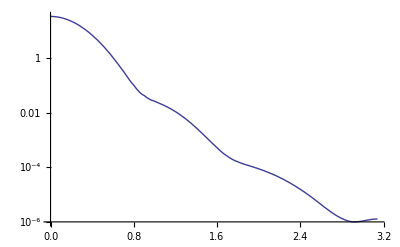

```mathematica
p1=LogPlot[interp1[θ],{θ,0,Pi}]
```

## Eikonal Approximation

These equations come straight out of Sakurai, equations 7.4.13 and 7.4.14 (page 394).

```mathematica
χ0exact[k_,b_]=-2*m/(k*(ℏc)^2)*NIntegrate[V[Sqrt[b^2+z^2]],{z,0,15}];
```

I had to have the iteration of the table below happen in integer steps because doing it in decimal steps was giving Mathematica problems somehow. I think it probably has something to do with differences in the way it handles integers and floats.

```mathematica
Table[{{k,b},χ0exact[k,b]},{b,0,15,.1},{k,Sqrt[100+2 m 10]/ℏc,Sqrt[1000^2+2 m 1000]/ℏc,.05}]
```

{{{{0.696061,0.},4.87954+0.975908 ⅈ},{{0.746061,0.},4.55252+0.910504 ⅈ},«154»,{{8.49606,0.},0.399768+0.0799537 ⅈ},{{8.54606,0.},0.397429+0.0794859 ⅈ}},{«1»},«147»,{{{«19»,14.9},«24»+«1»},«157»},{«1»}}

```mathematica
χ0approx=Interpolation[Flatten[%,1]];
```

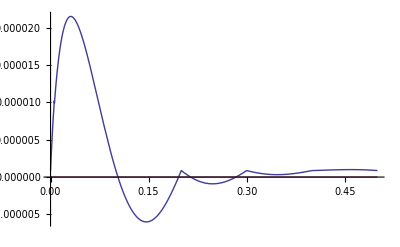

```mathematica
Plot[{Re[(χ0exact[1,b]-χ0approx[1,b])/χ0approx[1,b]],Im[(χ0exact[1,b]-χ0approx[1,b])/χ0approx[1,b]]},{b,0,.5},PlotRange->All]
```

```mathematica
T0[k_,b_]:=Exp[I*χ0approx[k,b]]-1
Eif0[k_,θ_]:=-I*k*NIntegrate[b*BesselJ[0,2*k*b*Sin[θ/2]]*T0[k,b],{b,0,15}]
```

```mathematica
σT[En_]:=10*4*Pi/(Sqrt[En^2+2*m*En]/ℏc)*Im[f[Sqrt[En^2+2*m*En]/ℏc,0]];
```

```mathematica
σT[375]
```

62.3631

```mathematica
σTplot=Interpolation[Table[{En,σT[En]},{En,10,1000,10}]];
```

```mathematica
σTEi0[En_]:=10*4*Pi/(Sqrt[En^2+2*m*En]/ℏc)*Im[Eif0[Sqrt[En^2+2*m*En]/ℏc,0]];
```

```mathematica
σTEi0[375]
```

61.5972

```mathematica
Table[{En,σTEi0[En]},{En,10,1000,10}]
```

{{10,514.686},{20,424.021},{30,353.675},{40,303.042},{50,265.592},{60,236.894},{70,214.209},{80,195.814},{90,180.579},{100,167.74},{110,156.762},{120,147.257},{130,138.941},{140,131.597},{150,125.059},{160,119.198},{170,113.91},{180,109.114},{190,104.74},{200,100.734},{210,97.0496},{220,93.6484},{230,90.4977},{240,87.5699},{250,84.8414},{260,82.2917},{270,79.9032},{280,77.6605},{290,75.5502},{300,73.5604},{310,71.6809},{320,69.9022},{330,68.2163},{340,66.6157},{350,65.094},{360,63.6452},{370,62.264},{380,60.9456},{390,59.6857},{400,58.4803},{410,57.3259},{420,56.2191},{430,55.157},{440,54.1368},{450,53.156},{460,52.2122},{470,51.3034},{480,50.4276},{490,49.5829},{500,48.7676},{510,47.9803},{520,47.2193},{530,46.4835},{540,45.7714},{550,45.082},{560,44.4141},{570,43.7668},{580,43.1389},{590,42.5298},{600,41.9384},{610,41.364},{620,40.8059},{630,40.2634},{640,39.7357},{650,39.2223},{660,38.7226},{670,38.2361},{680,37.7621},{690,37.3002},{700,36.8499},{710,36.4109},{720,35.9826},{730,35.5646},{740,35.1566},{750,34.7583},{760,34.3692},{770,33.989},{780,33.6175},{790,33.2542},{800,32.8991},{810,32.5516},{820,32.2117},{830,31.8791},{840,31.5535},{850,31.2347},{860,30.9225},{870,30.6166},{880,30.3169},{890,30.0233},{900,29.7354},{910,29.4531},{920,29.1763},{930,28.9049},{940,28.6385},{950,28.3772},{960,28.1207},{970,27.8689},{980,27.6218},{990,27.379},{1000,27.1407}}

```mathematica
σTEi0plot=Interpolation[%];
```

InterpolatingFunction::dmval: Input value {2.30268} lies outside the range of data in the interpolating function. Extrapolation will be used.

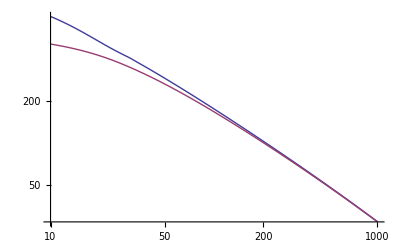

```mathematica
LogLogPlot[{σTplot[En],σTEi0plot[En]},{En,10,1000}]
```

It is clear from the above graph that the Eikonal approximation breaks down as an estimate of the σtotal below about 100 MeV for this particular potential. That corresponds to a value of E/|V0| ~= 2.4. We could (and probably should) test this ratio and see if it seems independent of |V0|.

```mathematica
100/Abs[V0]
```

2.36285

```mathematica
eik0dσdΩ[En_,points_:10]:=Table[{N[θ/points],Abs[Eif0[Sqrt[En^2+2*m*En]/ℏc,θ/points]]^2},{θ,0,points*Pi,1}]
```

```mathematica
eik0dσdΩ[100]
```

{{0.,32.5612},{0.1,29.4239},{0.2,21.8047},{0.3,13.4054},{0.4,6.9497},{0.5,3.098},{0.6,1.21891},{0.7,0.443616},{0.8,0.163943},{0.9,0.0700775},{1.,0.0364227},{1.1,0.0211144},{1.2,0.0123674},{1.3,0.00701102},{1.4,0.00383142},{1.5,0.0020469},{1.6,0.00109317},{1.7,0.00059864},{1.8,0.000343883},{1.9,0.000210075},{2.,0.000136719},{2.1,0.0000941194},{2.2,0.0000678615},{2.3,0.0000508285},{2.4,0.0000393534},{2.5,0.0000314285},{2.6,0.000025881},{2.7,0.0000219881},{2.8,0.0000192886},{2.9,0.0000174844},{3.,0.0000163869},{3.1,0.0000158855}}

```mathematica
eik0interp1=Interpolation[%]
```

InterpolatingFunction[{{0.,3.1}},<>]

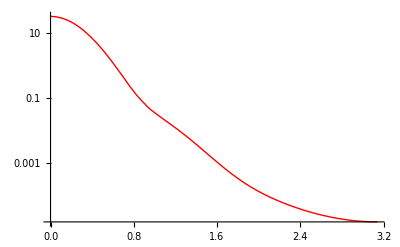

```mathematica
eik0p1=LogPlot[eik0interp1[θ],{θ,0,Pi},PlotStyle->Red]
```

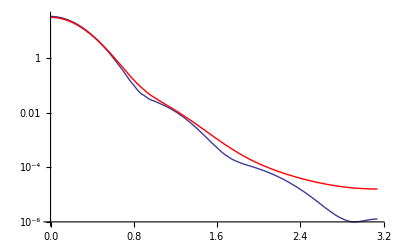

```mathematica
Show[p1,eik0p1]
```

As you can see above, the two plots actually agree with each other pretty well, especially at small θ. There is some pretty obvious disagreement for large θ, however, and the eikonal approximation seems to miss some of the structure apparent in the partial wave formulation.

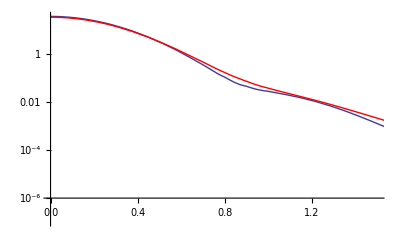

```mathematica
Show[p1,eik0p1,PlotRange->{{0,1.5},{Log[10^-7],Log[35]}}]
```

## Add in Eikonal Corrections

### First order correction

Below are parameters used by Wallace in his treatment of this:

```mathematica
En[k_]:=-m+Sqrt[m^2+(k*ℏc)^2]
U[r_]:=V[r]/V0
ϵ[k_]:=V0/(2*En[k])
```

```mathematica
τ1exact[k_,b_]=-k*ϵ[k]^2*NIntegrate[Evaluate[(1#+b*D[#,b])&[U[Sqrt[z^2+b^2]]^2]],{z,0,15}];
```

NIntegrate::inumr: The integrand 1.  + 5.55112×10^-17\ ⅈ/(1 + ⅇ^1.85185\ (-« 19 » + « 1 »))^2 - (3.7037  + 2.05597×10^-16\ ⅈ)\ b^2\ ⅇ^1.85185\ (-« 19 » + √« 1 »)/(1 + ⅇ^1.85185\ « 1 »)^3\ √b^2 + z^2
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 15}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

```mathematica
Table[{{k,b},τ1exact[k,b]},{b,0,15,.05},{k,Sqrt[100+2 m 10]/ℏc,Sqrt[1000^2+2 m 1000]/ℏc,.05}]
```

{{{{0.696061,0.},-3.39921-1.41634 ⅈ},{{0.746061,0.},-2.76489-1.15204 ⅈ},«154»,{{8.49606,0.},-0.00429442-0.00178934 ⅈ},{{8.54606,0.},-0.00424495-0.00176873 ⅈ}},{«1»},«298»,{{«1»,«23»+«23» ⅈ},«157»}}

```mathematica
{{}, {{{{{0.6960605635484076,0.},-3.399210241834009-1.4163376007641706 ⅈ},{{0.7460605635484077,0.},-2.7648887546983403-1.1520369811243087 ⅈ},«154»,{{8.496060563548408,0.},-0.004294418760283351-0.0017893411501180634 ⅈ},{{8.546060563548409,0.},-0.004244948746259835-0.0017687286442749316 ⅈ}},{«1»},{«1»},«295»,{«1»},{«1»},{«1»}}}, {}}
```

{{{{0.696061,0.},-3.39921-1.41634 ⅈ},{{0.746061,0.},-2.76489-1.15204 ⅈ},«154»,{{8.49606,0.},-0.00429442-0.00178934 ⅈ},{{8.54606,0.},-0.00424495-0.00176873 ⅈ}},{«1»},{«1»},«295»,{«1»},{«1»},{«1»}}

```mathematica
τ1approx=Interpolation[Flatten[%,1]];
```

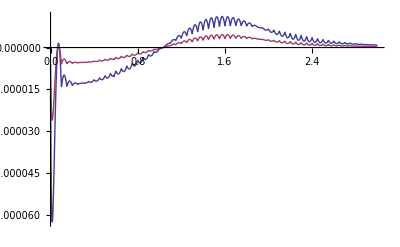

```mathematica
Plot[{Re[τ1exact[1,b]-τ1approx[1,b]],Im[τ1exact[1,b]-τ1approx[1,b]]},{b,0,3},PlotRange->All]
```

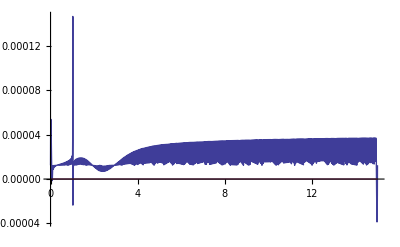

```mathematica
Plot[{Re[(τ1exact[1,b]-τ1approx[1,b])/τ1approx[1,b]],Im[(τ1exact[1,b]-τ1approx[1,b])/τ1approx[1,b]]},{b,0,15},PlotRange->All]
```

```mathematica
T1[k_,b_]:=Exp[I(χ0approx[k,b]+τ1approx[k,b])]-1
Eif1[k_,θ_]:=-I*k*NIntegrate[b*BesselJ[0,2*k*b*Sin[θ/2]]*T1[k,b],{b,0,15}]
```

```mathematica
eik1dσdΩ[En_,points_:10]:=Table[{N[θ/points],Abs[Eif1[Sqrt[En^2+2 m En]/ℏc,θ/points]]^2},{θ,0,points*Pi,1}]
```

```mathematica
σTEi1[En_]:=10*4*Pi/(Sqrt[En^2+2*m*En]/ℏc)*Im[Eif1[Sqrt[En^2+2*m*En]/ℏc,0]];
```

```mathematica
Table[{En,σTEi1[En]},{En,10,1000,10}]
```

{{10,648.77},{20,535.425},{30,422.051},{40,347.924},{50,297.204},{60,260.408},{70,232.44},{80,210.409},{90,192.563},{100,177.784},{110,165.322},{120,154.656},{130,145.411},{140,137.314},{150,130.155},{160,123.775},{170,118.049},{180,112.879},{190,108.184},{200,103.899},{210,99.9706},{220,96.3549},{230,93.0146},{240,89.9181},{250,87.0387},{260,84.3535},{270,81.8428},{280,79.4895},{290,77.2786},{300,75.1972},{310,73.2338},{320,71.3782},{330,69.6215},{340,67.9557},{350,66.3736},{360,64.8689},{370,63.4358},{380,62.0691},{390,60.7641},{400,59.5166},{410,58.3227},{420,57.179},{430,56.0822},{440,55.0294},{450,54.0179},{460,53.0452},{470,52.109},{480,51.2073},{490,50.3381},{500,49.4997},{510,48.6903},{520,47.9085},{530,47.1527},{540,46.4218},{550,45.7143},{560,45.0293},{570,44.3655},{580,43.722},{590,43.0979},{600,42.4922},{610,41.9041},{620,41.3329},{630,40.7778},{640,40.238},{650,39.713},{660,39.2022},{670,38.7049},{680,38.2206},{690,37.7488},{700,37.289},{710,36.8407},{720,36.4035},{730,35.977},{740,35.5608},{750,35.1544},{760,34.7576},{770,34.37},{780,33.9912},{790,33.6211},{800,33.2591},{810,32.9052},{820,32.559},{830,32.2202},{840,31.8886},{850,31.5641},{860,31.2462},{870,30.935},{880,30.63},{890,30.3312},{900,30.0384},{910,29.7513},{920,29.4698},{930,29.1937},{940,28.923},{950,28.6573},{960,28.3966},{970,28.1407},{980,27.8896},{990,27.643},{1000,27.4008}}

```mathematica
σTEi1plot=Interpolation[%];
```

InterpolatingFunction::dmval: Input value {2.30268} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

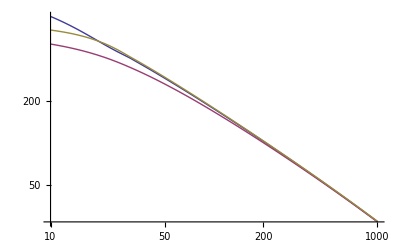

```mathematica
LogLogPlot[{σTplot[En],σTEi0plot[En],σTEi1plot[En]},{En,10,1000}]
```

```mathematica
eik1dσdΩ[100]
```

{{0.,35.4075},{0.1,31.9625},{0.2,23.5888},{0.3,14.3519},{0.4,7.2683},{0.5,3.0855},{0.6,1.10283},{0.7,0.338661},{0.8,0.10155},{0.9,0.0430369},{1.,0.0290186},{1.1,0.0215397},{1.2,0.0145713},{1.3,0.00882555},{1.4,0.00490523},{1.5,0.00259699},{1.6,0.00137715},{1.7,0.000776758},{1.8,0.000488168},{1.9,0.000343057},{2.,0.000260767},{2.1,0.000206589},{2.2,0.000166778},{2.3,0.000136036},{2.4,0.000112069},{2.5,0.0000935496},{2.6,0.0000794658},{2.7,0.0000689757},{2.8,0.0000613892},{2.9,0.0000561715},{3.,0.0000529387},{3.1,0.0000514468}}

```mathematica
eik1interp1=Interpolation[%];
```

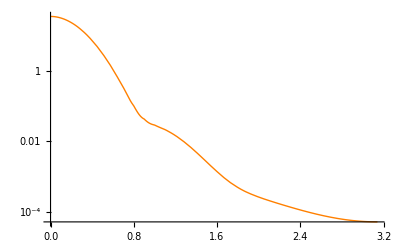

```mathematica
eik1p1=LogPlot[eik1interp1[θ],{θ,0,Pi},PlotStyle->Orange]
```

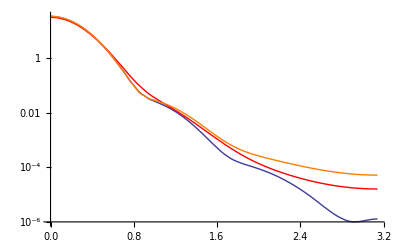

```mathematica
Show[p1,eik0p1,eik1p1]
```

### Second order correction

```mathematica
τ2exact[k_,b_]=-k*ϵ[k]^3*NIntegrate[Evaluate[(1#+5/3*b*D[#,b]+1/3*b^2*D[#,{b,2}])&[U[Sqrt[z^2+b^2]]^3]],{z,0,15}]-b*D[χ0exact[k,b],b]^3/(24*k^2);
ω2exact[k_,b_]=D[χ0exact[k,b],b]*D[b*D[χ0exact[k,b],b],b]/(8*k^2);
```

NIntegrate::inumr: The integrand 1.  + 8.32667×10^-17\ ⅈ/(1 + ⅇ^1.85185\ (-« 19 » + « 1 »))^3 - « 1 »/« 1 » + (0.333333  + 2.77556×10^-17\ ⅈ)\ b^2\ (5.55556\ b^2\ ⅇ^1.85185\ (-« 19 » + « 1 »)/(1 + ⅇ^Times[« 2 »])^4\ (b^2 + z^2)^3/2 + 41.1523\ « 1 »\ ⅇ^« 1 »/(1 + « 1 »)^5\ (b^2 + z^2) - « 1 »/« 1 »\ « 1 » - 5.55556\ ⅇ^« 19 »\ (« 1 »)/(1 + ⅇ^« 5 » « 1 » « 1 »])^4\ √b^2 + z^2)
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 15}}.

NIntegrate::inumr: The integrand -41.5  + 8.3\ ⅈ/1 + ⅇ^1.85185\ (-1.67444 + √Plus[« 2 »])
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 15}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand -41.5  + 8.3\ ⅈ/1 + ⅇ^1.85185\ (-1.67444 + √Plus[« 2 »])
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 15}}.

NIntegrate::inumr: The integrand (76.8519  + 15.3704\ ⅈ)\ b\ ⅇ^1.85185\ (-1.67444 + √b^2 + « 1 »)/(1 + ⅇ^1.85185\ (-« 19 » + √« 1 »))^2\ √b^2 + z^2
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 15}}.

NIntegrate::inumr: The integrand -41.5  + 8.3\ ⅈ/1 + ⅇ^1.85185\ (-1.67444 + √Plus[« 2 »])
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 15}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

```mathematica
Table[{{k,b},τ2exact[k,b]},{b,0,15,.05},{k,Sqrt[100+2 m 10]/ℏc,Sqrt[1000^2+2 m 1000]/ℏc,.05}]//Timing
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate :: izero will be suppressed during this calculation.

{821.242,{{{{0.696061,0.},5.11256+3.43936 ⅈ},{{0.746061,0.},3.62263+2.43704 ⅈ},«154»,{{8.49606,0.},0.0000657117+0.0000442061 ⅈ},{{8.54606,0.},0.0000643903+0.0000433171 ⅈ}},«299»,{«1»}}}

```mathematica
{{}, {{1229.8551829999997,{{{{0.6960605635484076,0.},5.1125600725708535+3.4393585942749385 ⅈ},{{0.7460605635484077,0.},3.622633089771865+2.437044078573801 ⅈ},«155»,{{8.546060563548409,0.},0.00006439032123641714+0.000043317125195407906 ⅈ}},{«1»},«598»,{{{0.6960605635484076,15.},2.2621539372650864*^-28+«23» ⅈ},«157»}}}}, {}}
```

{1229.86,{{{{0.696061,0.},5.11256+3.43936 ⅈ},{{0.746061,0.},3.62263+2.43704 ⅈ},«155»,{{8.54606,0.},0.0000643903+0.0000433171 ⅈ}},{«1»},«598»,{{{0.696061,15.},2.26215×10^-28+«23» ⅈ},«157»}}}

```mathematica
τ2approx=Interpolation[Flatten[%[[2]],1]];
```

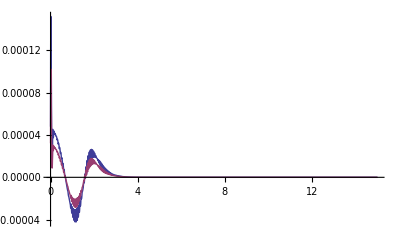

```mathematica
Plot[{Re[τ2exact[1,b]-τ2approx[1,b]],Im[τ2exact[1,b]-τ2approx[1,b]]},{b,0,15},PlotRange->All]
```

```mathematica
D[χ0[1,b],b]/.b->0
```

-0.00671382-0.00134276 ⅈ

```mathematica
D[χ0temp[1,b],b]*D[D[χ0temp[1,b],b],b]/.b->0.2/.b->0.2
```

NIntegrate::inumr: The integrand -41.5  + 8.3\ ⅈ/1 + ⅇ^1.85185\ (-1.67444 + √Plus[« 2 »])
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 15}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

0.440945+0.183727 ⅈ

NIntegrate::inumr: The integrand -41.5  + 8.3\ ⅈ/1 + ⅇ^1.85185\ (-1.67444 + √Plus[« 2 »])
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 15}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {2.85656×10^-8}. NIntegrate obtained 8.76966×10^-7 + 1.75393×10^-7\ ⅈ and 1.60477×10^-12 for the integral and error estimates.

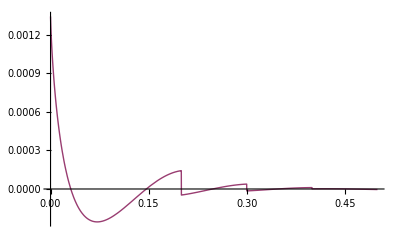

```mathematica
Plot[{Re[D[χ0temp[1,b],b]-D[χ0[1,b],b]]/.b->X,Im[D[χ0temp[1,b],b]-D[χ0[1,b],b]]/.b->x},{x,0,.5},PlotRange->All]
```

```mathematica
Join[Table[{{k,b},ω2exact[k,b]},{b,0,5,.1},{k,Sqrt[100+2 m 10]/ℏc,Sqrt[1000^2+2 m 1000]/ℏc,.05}],Table[{{k,x},D[χ0[k,b],b]*D[b*D[χ0[k,b],b],b]/(8*k^2)},{x,5.1,15,.1},{k,Sqrt[100+2 m 10]/ℏc,Sqrt[1000^2+2 m 1000]/ℏc,.05}]]//Timing
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {2.44609×10^-28}. NIntegrate obtained 1162.7  + 232.541\ ⅈ
 and 318.895 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate :: izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {2.44609×10^-28}. NIntegrate obtained 1162.7  + 232.541\ ⅈ
 and 318.895 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

{172.071,{{{{0.696061,0.},0.+0. ⅈ},{{0.746061,0.},0.+0. ⅈ},{{0.796061,0.},0.+0. ⅈ},{{0.846061,0.},0.+0. ⅈ},«151»,{{8.44606,0.},0.+0. ⅈ},{{8.49606,0.},0.+0. ⅈ},{{8.54606,0.},0.+0. ⅈ}},{«1»},{«1»},«145»,{«1»},{«1»},{«1»}}}

```mathematica
{{}, {{183.43135999999868,{{{{0.6960605635484076,0.},0.+0. ⅈ},{{0.7460605635484077,0.},0.+0. ⅈ},{{0.7960605635484076,0.},0.+0. ⅈ},«152»,{{8.446060563548407,0.},0.+0. ⅈ},{{8.496060563548408,0.},0.+0. ⅈ},{{8.546060563548409,0.},0.+0. ⅈ}},«149»,{«1»}}}}, {}}
```

%535

$OutputSizeLimit::nosess: This output can only be updated in the same kernel session that generated it.

```mathematica
Table[{b,ω2temp[1,b]},{b,0,5,.1}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {2.44609×10^-28}. NIntegrate obtained 1162.7  + 232.541\ ⅈ
 and 318.895 for the integral and error estimates.

{{0.,0.+0. ⅈ},{0.1,0.00653165+0.00272152 ⅈ},{0.2,0.0231123+0.00963011 ⅈ},{0.3,0.0485022+0.0202092 ⅈ},{0.4,0.0821293+0.0342205 ⅈ},{0.5,0.123312+0.0513799 ⅈ},{0.6,0.170901+0.071209 ⅈ},{0.7,0.223003+0.092918 ⅈ},{0.8,0.27676+0.115317 ⅈ},{0.9,0.32826+0.136775 ⅈ},{1.,0.372652+0.155272 ⅈ},{1.1,0.40454+0.168558 ⅈ},{1.2,0.418699+0.174458 ⅈ},{1.3,0.411032+0.171263 ⅈ},{1.4,0.379603+0.158168 ⅈ},{1.5,0.325425+0.135594 ⅈ},{1.6,0.252711+0.105296 ⅈ},{1.7,0.168386+0.0701608 ⅈ},{1.8,0.0809215+0.0337173 ⅈ},{1.9,-0.00122819-0.000511746 ⅈ},{2.,-0.0711191-0.029633 ⅈ},{2.1,-0.124334-0.0518057 ⅈ},{2.2,-0.159305-0.0663769 ⅈ},{2.3,-0.176985-0.0737439 ⅈ},{2.4,-0.1801-0.0750416 ⅈ},{2.5,-0.17226-0.0717748 ⅈ},{2.6,-0.157189-0.0654956 ⅈ},{2.7,-0.138191-0.0575796 ⅈ},{2.8,-0.117865-0.0491106 ⅈ},{2.9,-0.098047-0.0408529 ⅈ},{3.,-0.0798773-0.0332822 ⅈ},{3.1,-0.0639441-0.0266434 ⅈ},{3.2,-0.0504369-0.0210154 ⅈ},{3.3,-0.0392864-0.0163693 ⅈ},{3.4,-0.0302756-0.0126148 ⅈ},{3.5,-0.0231194-0.00963309 ⅈ},{3.6,-0.0175171-0.00729877 ⅈ},{3.7,-0.0131832-0.00549299 ⅈ},{3.8,-0.009864-0.00411 ⅈ},{3.9,-0.00734338-0.00305974 ⅈ},{4.,-0.00544292-0.00226788 ⅈ},{4.1,-0.00401883-0.00167451 ⅈ},{4.2,-0.00295734-0.00123222 ⅈ},{4.3,-0.00216974-0.000904059 ⅈ},{4.4,-0.00158769-0.000661538 ⅈ},{4.5,-0.00115904-0.000482933 ⅈ},{4.6,-0.000844327-0.000351803 ⅈ},{4.7,-0.000613894-0.000255789 ⅈ},{4.8,-0.000445578-0.000185658 ⅈ},{4.9,-0.000322901-0.000134542 ⅈ},{5.,-0.000233662-0.0000973592 ⅈ}}

```mathematica
{{}, {{{{{0.6960605635484076,0.},0.00002304270476362962+9.601126984846883*^-6 ⅈ},{{0.7460605635484077,0.},0.000017459235970421924+7.274681654324482*^-6 ⅈ},«154»,{{8.496060563548408,0.},1.0381286392747538*^-9+4.325535996974844*^-10 ⅈ},{{8.546060563548409,0.},1.0140461155084359*^-9+4.225192147951276*^-10 ⅈ}},«599»,{«1»}}}, {}}
```

{{{{0.696061,0.},0.0000230427+9.60113×10^-6 ⅈ},{{0.746061,0.},0.0000174592+7.27468×10^-6 ⅈ},«154»,{{8.49606,0.},1.03813×10^-9+4.32554×10^-10 ⅈ},{{8.54606,0.},1.01405×10^-9+4.22519×10^-10 ⅈ}},«599»,{«1»}}

```mathematica
ω2=Interpolation[Flatten[%[[2]],1]];
```

```mathematica
ω2temp[1,1.1]-ω2[1.1]
```

0.+0. ⅈ

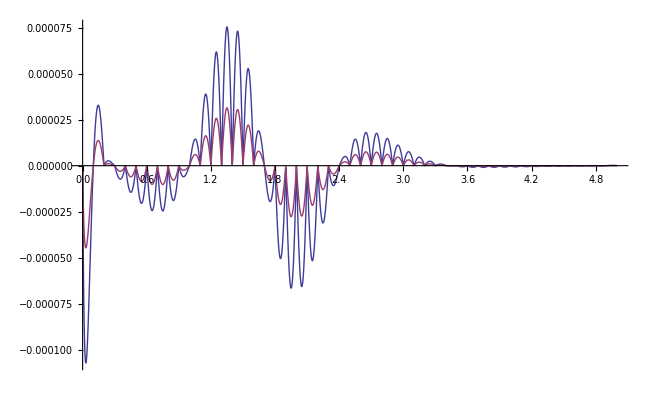

```mathematica
Plot[{Re[ω2temp[1,b]-ω2[b]],Im[ω2temp[1,b]-ω2[b]]},{b,0,5},PlotRange->All]
```

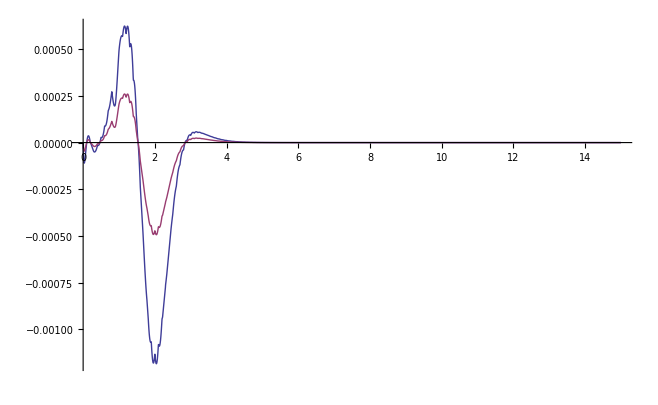

```mathematica
Plot[{Re[ω2temp[1,b]-ω2[1,b]],Im[ω2temp[1,b]-ω2[1,b]]},{b,0,15},PlotRange->All]
```

```mathematica
T2[k_,b_]:=Exp[I(χ0[k,b]+τ1[k,b]+τ2[k,b])]*Exp[-ω2[k,b]]-1
Eif2[k_,θ_]:=-I*k*NIntegrate[b*BesselJ[0,2*k*b*Sin[θ/2]]*T2[k,b],{b,0,15}]
```

```mathematica
eik2dσdΩ[En_,points_:10]:=Table[{N[θ/points],Abs[Eif2[Sqrt[En^2+2 m En]/ℏc,θ/points]]^2},{θ,0,points*Pi,1}]
```

```mathematica
σTEi2[En_]:=10*4*Pi/(Sqrt[En^2+2*m*En]/ℏc)*Im[Eif2[Sqrt[En^2+2*m*En]/ℏc,0]];
```

```mathematica
Table[{En,σTEi2[En]},{En,10,1000,10}]
```

{{10,600.23},{20,529.697},{30,414.043},{40,341.709},{50,292.779},{60,257.246},{70,230.13},{80,208.679},{90,191.237},{100,176.746},{110,164.495},{120,153.986},{130,144.861},{140,136.856},{150,129.77},{160,123.448},{170,117.769},{180,112.637},{190,107.973},{200,103.715},{210,99.8085},{220,96.2115},{230,92.8869},{240,89.804},{250,86.9363},{260,84.2612},{270,81.7593},{280,79.4137},{290,77.2097},{300,75.1343},{310,73.1761},{320,71.3253},{330,69.5728},{340,67.9107},{350,66.332},{360,64.8304},{370,63.4},{380,62.0358},{390,60.7331},{400,59.4876},{410,58.2957},{420,57.1537},{430,56.0584},{440,55.0071},{450,53.9969},{460,53.0254},{470,52.0904},{480,51.1897},{490,50.3215},{500,49.4839},{510,48.6754},{520,47.8943},{530,47.1393},{540,46.409},{550,45.7022},{560,45.0177},{570,44.3545},{580,43.7116},{590,43.0879},{600,42.4827},{610,41.895},{620,41.3242},{630,40.7694},{640,40.23},{650,39.7054},{660,39.1948},{670,38.6978},{680,38.2138},{690,37.7423},{700,37.2827},{710,36.8347},{720,36.3977},{730,35.9714},{740,35.5554},{750,35.1493},{760,34.7526},{770,34.3652},{780,33.9866},{790,33.6166},{800,33.2548},{810,32.901},{820,32.5549},{830,32.2163},{840,31.8848},{850,31.5604},{860,31.2427},{870,30.9315},{880,30.6267},{890,30.328},{900,30.0352},{910,29.7482},{920,29.4668},{930,29.1909},{940,28.9202},{950,28.6546},{960,28.394},{970,28.1382},{980,27.8871},{990,27.6405},{1000,27.3984}}

```mathematica
σTEi2Plot=Interpolation[%];
```

InterpolatingFunction::dmval: Input value {2.30268} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

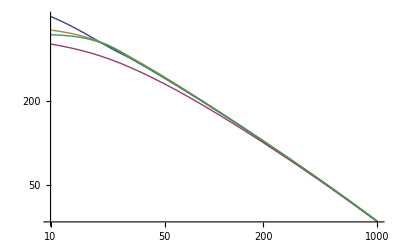

```mathematica
LogLogPlot[{σTplot[En],σTEiplot[En],σTEi1Plot[En],σTEi2Plot[En]},{En,10,1000}]
```

```mathematica
eik2dσdΩ[100]
```

{{0.,35.3318},{0.1,31.8768},{0.2,23.4855},{0.3,14.2457},{0.4,7.18224},{0.5,3.03198},{0.6,1.07873},{0.7,0.332499},{0.8,0.102327},{0.9,0.0443653},{1.,0.0288075},{1.1,0.0200045},{1.2,0.0125536},{1.3,0.0069789},{1.4,0.00351921},{1.5,0.00169632},{1.6,0.00086322},{1.7,0.000524976},{1.8,0.000393585},{1.9,0.000332422},{2.,0.000289011},{2.1,0.000248781},{2.2,0.000210602},{2.3,0.000176313},{2.4,0.000147283},{2.5,0.000123852},{2.6,0.000105639},{2.7,0.0000919361},{2.8,0.0000819902},{2.9,0.0000751466},{3.,0.0000709094},{3.1,0.0000689557}}

```mathematica
eik2interp1=Interpolation[%];
```

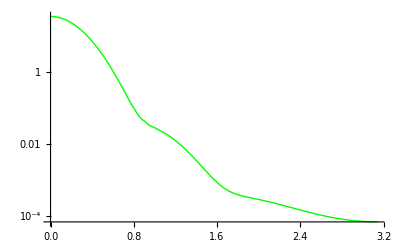

```mathematica
eik2p1=LogPlot[eik2interp1[θ],{θ,0,Pi},PlotStyle->Green]
```

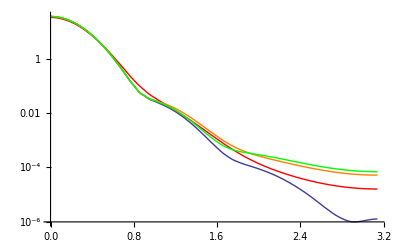

```mathematica
Show[p1,eik0p1,eik1p1,eik2p1,PlotRange->Automatic]
```

### Third order correction

```mathematica
τ3[k_,b_]=-k*ϵ[k]^4*NIntegrate[Evaluate[(5/4#+11/4*b*D[#,b]+b^2*D[#,{b,2}]+1/12*b^3*D[#,{b,3}])&[U[Sqrt[z^2+b^2]]^4]],{z,0,15}]-b*D[τ1[k,b],b]*D[χ0[k,b],b]^2/(8*k^2);
ϕ3[k_,b_]=-k*ϵ[k]^2*NIntegrate[Evaluate[(1#+5/3*b*D[#,b]+1/3*b^2*D[#,{b,2}])&[(1/(2*k)*D[U[Sqrt[z^2+b^2]],b])^2]],{z,0,15}];
ω3[k_,b_]=(D[χ0[k,b],b]*D[b*D[τ1[k,b],b],b]+D[τ1[k,b],b]*D[b*D[χ0[k,b],b],b])/(8*k^2);
```

```mathematica
T3[k_,b_]:=Exp[I*(χ0[k,b]+τ1[k,b]+τ2[k,b]+τ3[k,b]+ϕ3[k,b])]*Exp[-(ω2[k,b]+ω3[k,b])]-1
```

```mathematica
Eif3[k_,θ_]:=-I*k*NIntegrate[b*BesselJ[0,2*k*b*Sin[θ/2]]*T3[k,b],{b,0,15}]
```

```mathematica
eik3dσdΩ[En_,points_:10]:=Table[{N[θ/points],Abs[Eif3[Sqrt[En^2+2 m En]/ℏc,θ/points]]^2},{θ,0,points*Pi,1}]
```

```mathematica
σTEi3[En_]:=40 Pi/(Sqrt[En^2+2 m En]/ℏc) Im[Eif3[Sqrt[En^2+2 m En]/ℏc,0]]
```

```mathematica
Table[{En,σTEi3[En]},{En,10,1000,10}]
```

$Aborted

```mathematica
Plot[Re[τ3[Sqrt[10000+2 m 100]/ℏc,b]],{b,0,15}]
```

$Aborted

```mathematica
σTEi3[10]
```

NIntegrate::inumr: The integrand -41.5  + 8.3\ ⅈ/1 + ⅇ^1.85185\ (-1.67444 + √Plus[« 2 »])
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 15}}.

NIntegrate::inumr: The integrand 1.  + 5.55112×10^-17\ ⅈ/(1 + ⅇ^1.85185\ (-« 19 » + « 1 »))^2 - (3.7037  + 2.05597×10^-16\ ⅈ)\ b^2\ ⅇ^1.85185\ (-« 19 » + « 1 »)/(1 + ⅇ^1.85185\ « 1 »)^3\ √b^2 + z^2
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 15}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

803.563

```mathematica
σTEi3plot=Interpolation[%];
```

```mathematica
LogLogPlot[{(σTEiplot[En]-σTplot[En])/σTplot[En],(σTEi1Plot[En]-σTplot[En])/σTplot[En],(σTEi2Plot[En]-σTplot[En])/σTplot[En],(σTEi3plot[En]-σTplot[En])/σTplot[En]},{En,10,1000}]
```

```mathematica
eik3dσdΩ[100]
```

```mathematica
{{0,91.44454627711006},{0.1,86.93401462142639},{0.2,74.63539942644337},{0.30000000000000004,57.73580994872822},{0.4,40.1191611488699},{0.5,25.01154909387827},{0.6000000000000001,14.137423616688872},{0.7000000000000001,7.628404129429616},{0.8,4.517113985599908},{0.9,3.4373177523439993},{1.,3.191026845603401},{1.1,3.025041125904266},{1.2000000000000002,2.6393069732410597},{1.3,2.04368047822072},{1.4000000000000001,1.3836954073218313},{1.5,0.8100455864643781},{1.6,0.41410762975043075},{1.7000000000000002,0.21737791131140125},{1.8,0.19041266794593914},{1.9000000000000001,0.27971259914912966},{2.,0.4297942445530772},{2.1,0.5960371098986682},{2.2,0.7491310507723384},{2.3000000000000003,0.8740401298795031},{2.4000000000000004,0.966433394680398},{2.5,1.028668140282196},{2.6,1.066427761430172},{2.7,1.0863750659977414},{2.8000000000000003,1.0947558839109996},{2.9000000000000004,1.0967122891307253},{3.,1.096041229838605},{3.1,1.0951810613831496}}
```

{{0,91.4445},{0.1,86.934},{0.2,74.6354},{0.3,57.7358},{0.4,40.1192},{0.5,25.0115},{0.6,14.1374},{0.7,7.6284},{0.8,4.51711},{0.9,3.43732},{1.,3.19103},{1.1,3.02504},{1.2,2.63931},{1.3,2.04368},{1.4,1.3837},{1.5,0.810046},{1.6,0.414108},{1.7,0.217378},{1.8,0.190413},{1.9,0.279713},{2.,0.429794},{2.1,0.596037},{2.2,0.749131},{2.3,0.87404},{2.4,0.966433},{2.5,1.02867},{2.6,1.06643},{2.7,1.08638},{2.8,1.09476},{2.9,1.09671},{3.,1.09604},{3.1,1.09518}}

```mathematica
eik3interp1=Interpolation[%];
```

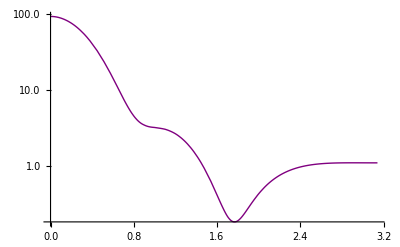

```mathematica
eik3p1=LogPlot[eik3interp1[θ],{θ,0,Pi},PlotStyle->Purple]
```

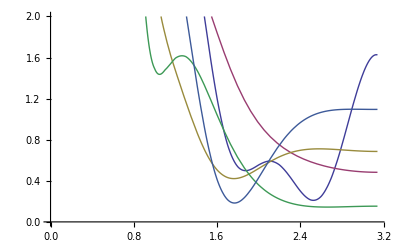

```mathematica
Plot[{interp1[θ],eik0interp1[θ],eik1interp1[θ],eik2interp1[θ],eik3interp1[θ]},{θ,0,π},PlotRange->{0,2}]
```

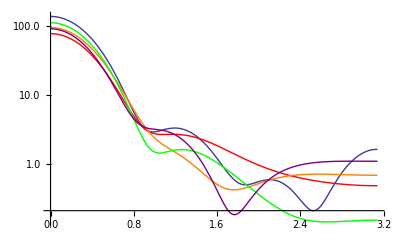

```mathematica
Show[p1,eik0p1,eik1p1,eik2p1,eik3p1,PlotRange->Automatic]
```

### Eikonal to third order for k = 1, 2, 3

```mathematica
eik1dσdΩ[2]
```

```mathematica
{{0,293.22916757681776},{0.1,253.73708442891774},{0.2,163.54525083771438},{0.30000000000000004,77.12185874818907},{0.4,25.827549639078388},{0.5,6.470193765582039},{0.6000000000000001,2.404829314396261},{0.7000000000000001,1.9708446558230917},{0.8,1.4418483020129758},{0.9,0.7725091233405128},{1.,0.3469346095016307},{1.1,0.17920260076861255},{1.2000000000000002,0.12740509798030303},{1.3,0.09836042734065897},{1.4000000000000001,0.06913635577519377},{1.5,0.044201145819914786},{1.6,0.027723797564798387},{1.7000000000000002,0.01858997815221487},{1.8,0.01371874720343962},{1.9000000000000001,0.010736034325405947},{2.,0.00851044754298138},{2.1,0.0066970413471289306},{2.2,0.005241989043030437},{2.3000000000000003,0.004130130923060545},{2.4000000000000004,0.003317940686099176},{2.5,0.0027421904266382103},{2.6,0.0023402945942820387},{2.7,0.0020618251899269546},{2.8000000000000003,0.0018709300822241403},{2.9000000000000004,0.0017441597963126962},{3.,0.0016671795249573332},{3.1,0.0016319996781983062}}
```

{{0,293.229},{0.1,253.737},{0.2,163.545},{0.3,77.1219},{0.4,25.8275},{0.5,6.47019},{0.6,2.40483},{0.7,1.97084},{0.8,1.44185},{0.9,0.772509},{1.,0.346935},{1.1,0.179203},{1.2,0.127405},{1.3,0.0983604},{1.4,0.0691364},{1.5,0.0442011},{1.6,0.0277238},{1.7,0.01859},{1.8,0.0137187},{1.9,0.010736},{2.,0.00851045},{2.1,0.00669704},{2.2,0.00524199},{2.3,0.00413013},{2.4,0.00331794},{2.5,0.00274219},{2.6,0.00234029},{2.7,0.00206183},{2.8,0.00187093},{2.9,0.00174416},{3.,0.00166718},{3.1,0.001632}}

```mathematica
eik1interp2=Interpolation[%];
```

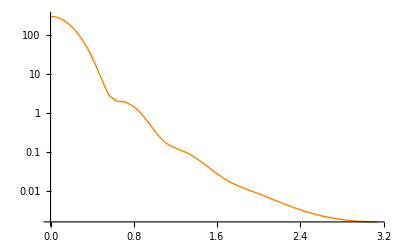

```mathematica
eik1p2=LogPlot[eik1interp2[θ],{θ,0,Pi},PlotStyle->Orange]
```

```mathematica
eik2dσdΩ[2]
```

```mathematica
{{0,294.8910610420141},{0.1,254.64906314911445},{0.2,163.0438766536933},{0.30000000000000004,75.93509962321531},{0.4,24.995469770821455},{0.5,6.304885592324231},{0.6000000000000001,2.5700573876368416},{0.7000000000000001,2.0945827457899067},{0.8,1.4219824225411097},{0.9,0.684685732267747},{1.,0.2732260646789869},{1.1,0.14396253329387548},{1.2000000000000002,0.1179262007797158},{1.3,0.09744344816721406},{1.4000000000000001,0.0684080785672247},{1.5,0.04267666743910603},{1.6,0.026908537622400235},{1.7000000000000002,0.019553362451643495},{1.8,0.01646813408118401},{1.9000000000000001,0.014645895152346293},{2.,0.012856322382081679},{2.1,0.01094820113938691},{2.2,0.009122353927508044},{2.3000000000000003,0.007560083105323252},{2.4000000000000004,0.006329439588063352},{2.5,0.005411916311465128},{2.6,0.004750752991457766},{2.7,0.004284532348888232},{2.8000000000000003,0.003962528625692157},{2.9000000000000004,0.0037483595712716152},{3.,0.0036184361539684435},{3.1,0.0035591384191706516}}
```

{{0,294.891},{0.1,254.649},{0.2,163.044},{0.3,75.9351},{0.4,24.9955},{0.5,6.30489},{0.6,2.57006},{0.7,2.09458},{0.8,1.42198},{0.9,0.684686},{1.,0.273226},{1.1,0.143963},{1.2,0.117926},{1.3,0.0974434},{1.4,0.0684081},{1.5,0.0426767},{1.6,0.0269085},{1.7,0.0195534},{1.8,0.0164681},{1.9,0.0146459},{2.,0.0128563},{2.1,0.0109482},{2.2,0.00912235},{2.3,0.00756008},{2.4,0.00632944},{2.5,0.00541192},{2.6,0.00475075},{2.7,0.00428453},{2.8,0.00396253},{2.9,0.00374836},{3.,0.00361844},{3.1,0.00355914}}

```mathematica
eik2interp2=Interpolation[%];
```

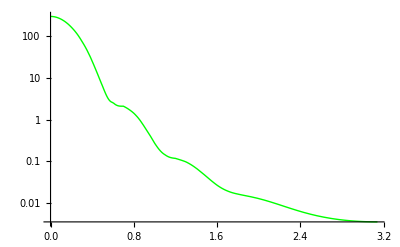

```mathematica
eik2p2=LogPlot[eik2interp2[θ],{θ,0,Pi},PlotStyle->Green]
```

```mathematica
eik3dσdΩ[2]
```

```mathematica
{{0,294.86691456514865},{0.1,254.72568209257432},{0.2,163.3026128276939},{0.30000000000000004,76.26132870351331},{0.4,25.23290700858881},{0.5,6.396043386339652},{0.6000000000000001,2.5518405487150866},{0.7000000000000001,2.031782755927383},{0.8,1.3639402190579146},{0.9,0.6519501171856685},{1.,0.26136665900409967},{1.1,0.13815228081376424},{1.2000000000000002,0.10790737102051179},{1.3,0.08268003362366579},{1.4000000000000001,0.053761303230222456},{1.5,0.032256482613916955},{1.6,0.021524363471284717},{1.7000000000000002,0.017681889654967888},{1.8,0.01617669761158569},{1.9000000000000001,0.014717166618473682},{2.,0.012906519213103873},{2.1,0.011067812566862553},{2.2,0.009514511180635484},{2.3000000000000003,0.008353938975641188},{2.4000000000000004,0.007544120654285952},{2.5,0.0069908764873193785},{2.6,0.006607264957444925},{2.7,0.006333323810317747},{2.8000000000000003,0.00613449966297479},{2.9000000000000004,0.005993551971246569},{3.,0.005903002447388051},{3.1,0.005860089596276548}}
```

{{0,294.867},{0.1,254.726},{0.2,163.303},{0.3,76.2613},{0.4,25.2329},{0.5,6.39604},{0.6,2.55184},{0.7,2.03178},{0.8,1.36394},{0.9,0.65195},{1.,0.261367},{1.1,0.138152},{1.2,0.107907},{1.3,0.08268},{1.4,0.0537613},{1.5,0.0322565},{1.6,0.0215244},{1.7,0.0176819},{1.8,0.0161767},{1.9,0.0147172},{2.,0.0129065},{2.1,0.0110678},{2.2,0.00951451},{2.3,0.00835394},{2.4,0.00754412},{2.5,0.00699088},{2.6,0.00660726},{2.7,0.00633332},{2.8,0.0061345},{2.9,0.00599355},{3.,0.005903},{3.1,0.00586009}}

```mathematica
eik3interp2=Interpolation[%];
```

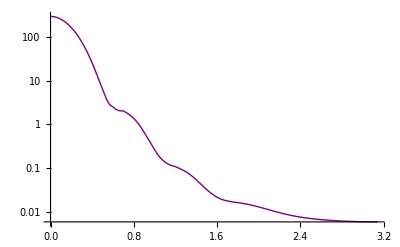

```mathematica
eik3p2=LogPlot[eik3interp2[θ],{θ,0,Pi},PlotStyle->Purple]
```

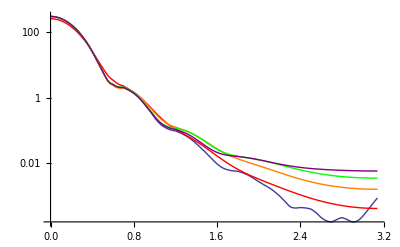

```mathematica
Show[p2,eik0p2,eik1p2,eik2p2,eik3p2,PlotRange->Automatic]
```

```mathematica
eik1dσdΩ[3,100]
```

```mathematica
{{0.,374.13781381048307},{0.01,372.9924352365846},{0.02,369.5764944900654},{0.03,363.94999741306157},{0.04,356.2110466279768},{0.05,346.4930607284497},{0.06,334.96103659736303},{0.07,321.80700061346386},{0.08,307.24482302297866},{0.09,291.50458960011684},{0.1,274.82673516963416},{0.11,257.45614445108004},{0.12,239.6364173953523},{0.13,221.6044796065673},{0.14,203.58569487788586},{0.15,185.78960792767757},{0.16,168.4064128968459},{0.17,151.6042089149153},{0.18,135.52706986015446},{0.19,120.29392296554035},{0.2,105.99820155234163},{0.21,92.70821199963676},{0.22,80.46813484073157},{0.23,69.29956503526144},{0.24,59.203487093034816},{0.25,50.162576626469686},{0.26,42.143720642228345},{0.27,35.10065382731625},{0.28,28.97661648296383},{0.29,23.706950795770805},{0.3,19.221564971846327},{0.31,15.44720859514822},{0.32,12.309516672785195},{0.33,9.734793561826066},{0.34,7.651520812372226},{0.35,5.991584510657416},{0.36,4.691227686393697},{0.37,3.691741597780101},{0.38,2.9399161685463358},{0.39,2.3882745513509676},{0.4,1.9951198370331393},{0.41,1.7244234705083015},{0.42,1.5455851685966986},{0.43,1.433093274959512},{0.44,1.3661127556954116},{0.45,1.32802565436674},{0.46,1.3059459930934698},{0.47,1.2902280132581372},{0.48,1.273983457849327},{0.49,1.252620443791906},{0.5,1.2234134659928246},{0.51,1.185111298096398},{0.52,1.1375870661985075},{0.53,1.0815326068528885},{0.54,1.0181973960965458},{0.55,0.9491708522420836},{0.56,0.8762056590503844},{0.57,0.8010789053633993},{0.58,0.7254872622200904},{0.59,0.6509720856036946},{0.6,0.5788702055676518},{0.61,0.5102862042913494},{0.62,0.4460821611474568},{0.63,0.38688111898197636},{0.64,0.3330808724171769},{0.65,0.2848750695543306},{0.66,0.2422790302746418},{0.67,0.20515809859611783},{0.68,0.17325674821330506},{0.69,0.14622703795249603},{0.7,0.12365535918915212},{0.71,0.1050867249365385},{0.72,0.09004611743494878},{0.73,0.07805663681438461},{0.74,0.0686543785924728},{0.75,0.06140011450413567},{0.76,0.05588796247212293},{0.77,0.05175131107633176},{0.78,0.048666315682653546},{0.79,0.04635331160570944},{0.8,0.04457649842034246},{0.81,0.04314224273393081},{0.82,0.04189632804472823},{0.83,0.04072045301591003},{0.84,0.03952824650641681},{0.85,0.03826103147644478},{0.86,0.03688353249704382},{0.87,0.03537968469075286},{0.88,0.03374866679545727},{0.89,0.03200124861326495},{0.9,0.030156514017714797},{0.91,0.02823899531988171},{0.92,0.02627623329659005},{0.93,0.02429675954015907},{0.94,0.022328483845796464},{0.95,0.020397458845633525},{0.96,0.018526986697175844},{0.97,0.01673702798124516},{0.98,0.015043870611082113},{0.99,0.013460016200984457},{1.,0.011994242487147167},{1.01,0.010651802773902999},{1.02,0.00943472661169807},{1.03,0.008342189727633243},{1.04,0.007370925371520464},{1.05,0.006515653497712485},{1.06,0.005769508405782452},{1.07,0.005124449482044743},{1.08,0.00457164336777611},{1.09,0.004101809367571587},{1.1,0.0037055226730064073},{1.11,0.003373472725044936},{1.12,0.0030966760385517885},{1.13,0.0028666445673546873},{1.14,0.0026755120128801524},{1.15,0.002516121459262672},{1.16,0.002382078384975052},{1.17,0.0022677734956340406},{1.18,0.0021683799947550425},{1.19,0.002079829866296656},{1.2,0.0019987736029421924},{1.21,0.0019225274935317342},{1.22,0.0018490122354803114},{1.23,0.001776686210261392},{1.24,0.0017044763124666972},{1.25,0.0016317087664055126},{1.26,0.001558041917243974},{1.27,0.0014834025581129092},{1.28,0.0014079269608863294},{1.29,0.0013319074229608627},{1.3,0.00125574482826694},{1.31,0.001179907451888439},{1.32,0.0011048960114723064},{1.33,0.0010312147860155215},{1.34,0.0009593484793300845},{1.35,0.0008897443994958891},{1.36,0.0008227994520112325},{1.37,0.0007588514000881523},{1.38,0.000698173825452878},{1.39,0.0006409742235693248},{1.4,0.0005873946843521528},{1.41,0.0005375146390759511},{1.42,0.0004913551936413724},{1.43,0.00044888461389927303},{1.44,0.00041002457839715964},{1.45,0.0003746568650888102},{1.46,0.00034263018950239687},{1.47,0.00031376696134726546},{1.48,0.0002878697731002793},{1.49,0.00026472747711808704},{1.5,0.0002441207468333636},{1.51,0.00022582705188706483},{1.52,0.0002096250070472521},{1.53,0.000195298079948174},{1.54,0.00018263766361696762},{1.55,0.00017144553654395317},{1.56,0.00016153574591318997},{1.57,0.00015273595916029061},{1.58,0.00014488833543288378},{1.59,0.00013784997233661647},{1.6,0.00013149298492851834},{1.61,0.00012570427358040584},{1.62,0.00012038503565684614},{1.63,0.00011545007291079895},{1.64,0.00011082694280896875},{1.65,0.00010645499758575926},{1.66,0.00010228435013598425},{1.67,0.00009827480093362979},{1.68,0.00009439475531884178},{1.69,0.00009062015572720753},{1.7,0.00008693344890793408},{1.71,0.00008332260397502475},{1.72,0.00007978019327799979},{1.73,0.00007630254461065219},{1.74,0.00007288897024033877},{1.75,0.00006954107557468509},{1.76,0.00006626214805464615},{1.77,0.00006305662501261661},{1.78,0.000059929637719374393},{1.79,0.00005688662769544341},{1.8,0.00005393303045770977},{1.81,0.000051074021319344144},{1.82,0.00004831431742963491},{1.83,0.000045658030105031},{1.84,0.00004310856145087499},{1.85,0.00004066853943945167},{1.86,0.0000383397857852157},{1.87,0.000036123311322701796},{1.88,0.00003401933391993781},{1.89,0.00003202731439733517},{1.9,0.000030146006355326973},{1.91,0.00002837351624143235},{1.92,0.00002670737046360616},{1.93,0.000025144586748307942},{1.94,0.000023681747391665144},{1.95,0.000022315072412021223},{1.96,0.00002104049099582404},{1.97,0.000019853709934064645},{1.98,0.00001875027805781317},{1.99,0.000017725645947207206},{2.,0.000016775220400778822},{2.01,0.000015894413372095567},{2.02,0.000015078685237040635},{2.03,0.00001432358239754933},{2.04,0.000013624769351765768},{2.05,0.00001297805544160433},{2.06,0.000012379416561835767},{2.07,0.000011825012178987175},{2.08,0.000011311198024851166},{2.09,0.000010834534865629102},{2.1,0.000010391793754054061},{2.11,9.97995816971786*^-6},{2.12,9.596223445493942*^-6},{2.13,9.237993866898316*^-6},{2.14,8.90287780530345*^-6},{2.15,8.588681230546763*^-6},{2.16,8.29339991607754*^-6},{2.17,8.015210626896435*^-6},{2.18,7.752461550641712*^-6},{2.19,7.5036622054027776*^-6},{2.2,7.267473029204065*^-6},{2.21,7.042694830470899*^-6},{2.22,6.828258253615334*^-6},{2.23,6.623213389064334*^-6},{2.24,6.4267196366751305*^-6},{2.25,6.238035909844821*^-6},{2.26,6.056511250204012*^-6},{2.27,5.881575905616361*^-6},{2.28,5.712732910649383*^-6},{2.29,5.549550193974073*^-6},{2.3,5.39165322846207*^-6},{2.31,5.238718227336146*^-6},{2.32,5.090465884442379*^-6},{2.33,4.946655647745902*^-6},{2.34,4.807080510816015*^-6},{2.35,4.671562303049519*^-6},{2.36,4.539947453943757*^-6},{2.37,4.412103207813111*^-6},{2.38,4.287914258411379*^-6},{2.39,4.167279779937592*^-6},{2.4,4.050110819655479*^-6},{2.41,3.936328028088194*^-6},{2.42,3.825859695057879*^-6},{2.43,3.718640066516616*^-6},{2.44,3.614607912793669*^-6},{2.45,3.5137053252808508*^-6},{2.46,3.415876715514762*^-6},{2.47,3.321067993814342*^-6},{2.48,3.2292259094319747*^-6},{2.49,3.1402975268404718*^-6},{2.5,3.0542298271693475*^-6},{2.51,2.9709694106459518*^-6},{2.52,2.890462291572651*^-6},{2.53,2.8126537682869318*^-6},{2.54,2.7374883563500615*^-6},{2.55,2.6649097755180056*^-6},{2.56,2.5948609796527875*^-6},{2.57,2.5272842198543525*^-6},{2.58,2.462121136138791*^-6},{2.59,2.3993128682008456*^-6},{2.6,2.3388001810505997*^-6},{2.61,2.2805236011963723*^-6},{2.62,2.2244235570395035*^-6},{2.63,2.170440522547907*^-6},{2.64,2.118515159701264*^-6},{2.65,2.0685884578360143*^-6},{2.66,2.0206018678021595*^-6},{2.67,1.9744974301280723*^-6},{2.68,1.930217856709785*^-6},{2.69,1.8877068371601331*^-6},{2.7,1.8469087515858066*^-6},{2.71,1.8077691545276731*^-6},{2.72,1.7702346644665048*^-6},{2.73,1.7342530773965652*^-6},{2.74,1.699773432362758*^-6},{2.75,1.666746067765194*^-6},{2.76,1.635122670054504*^-6},{2.77,1.60485631327189*^-6},{2.78,1.575901490941244*^-6},{2.79,1.5482141404176185*^-6},{2.8,1.5217516625246547*^-6},{2.81,1.4964729315250052*^-6},{2.82,1.4723383026893022*^-6},{2.83,1.4493096127107432*^-6},{2.84,1.4273501764771552*^-6},{2.85,1.4064247793830025*^-6},{2.86,1.386499665568198*^-6},{2.87,1.367542524564904*^-6},{2.88,1.3495224731824753*^-6},{2.89,1.3324100364395575*^-6},{2.9,1.3161771262264318*^-6},{2.91,1.3007970184872924*^-6},{2.92,1.2862443290194142*^-6},{2.93,1.2724949886628773*^-6},{2.94,1.2595262176135573*^-6},{2.95,1.2473164995767737*^-6},{2.96,1.2358455563326112*^-6},{2.97,1.225094321209125*^-6},{2.98,1.2150449139941128*^-6},{2.99,1.2056806162311343*^-6},{3.,1.1969858467505951*^-6},{3.01,1.1889461383649954*^-6},{3.02,1.1815481156191036*^-6},{3.03,1.174779473563935*^-6},{3.04,1.168628957229333*^-6},{3.05,1.1630863437324002*^-6},{3.06,1.1581424237223199*^-6},{3.07,1.153788986216142*^-6},{3.08,1.1500188042603705*^-6},{3.09,1.1468256211165255*^-6},{3.1,1.1442041399013494*^-6},{3.11,1.1421500134885433*^-6},{3.12,1.1406598362979838*^-6},{3.13,1.1397311385476292*^-6},{3.14,1.1393623810656883*^-6}}
```

{{0.,374.138},{0.01,372.992},{0.02,369.576},{0.03,363.95},{0.04,356.211},{0.05,346.493},{0.06,334.961},{0.07,321.807},{0.08,307.245},{0.09,291.505},{0.1,274.827},{0.11,257.456},{0.12,239.636},{0.13,221.604},{0.14,203.586},{0.15,185.79},{0.16,168.406},{0.17,151.604},{0.18,135.527},{0.19,120.294},{0.2,105.998},{0.21,92.7082},{0.22,80.4681},{0.23,69.2996},{0.24,59.2035},{0.25,50.1626},{0.26,42.1437},{0.27,35.1007},{0.28,28.9766},{0.29,23.707},{0.3,19.2216},{0.31,15.4472},{0.32,12.3095},{0.33,9.73479},{0.34,7.65152},{0.35,5.99158},{0.36,4.69123},{0.37,3.69174},{0.38,2.93992},{0.39,2.38827},{0.4,1.99512},{0.41,1.72442},{0.42,1.54559},{0.43,1.43309},{0.44,1.36611},{0.45,1.32803},{0.46,1.30595},{0.47,1.29023},{0.48,1.27398},{0.49,1.25262},{0.5,1.22341},{0.51,1.18511},{0.52,1.13759},{0.53,1.08153},{0.54,1.0182},{0.55,0.949171},{0.56,0.876206},{0.57,0.801079},{0.58,0.725487},{0.59,0.650972},{0.6,0.57887},{0.61,0.510286},{0.62,0.446082},{0.63,0.386881},{0.64,0.333081},{0.65,0.284875},{0.66,0.242279},{0.67,0.205158},{0.68,0.173257},{0.69,0.146227},{0.7,0.123655},{0.71,0.105087},{0.72,0.0900461},{0.73,0.0780566},{0.74,0.0686544},{0.75,0.0614001},{0.76,0.055888},{0.77,0.0517513},{0.78,0.0486663},{0.79,0.0463533},{0.8,0.0445765},{0.81,0.0431422},{0.82,0.0418963},{0.83,0.0407205},{0.84,0.0395282},{0.85,0.038261},{0.86,0.0368835},{0.87,0.0353797},{0.88,0.0337487},{0.89,0.0320012},{0.9,0.0301565},{0.91,0.028239},{0.92,0.0262762},{0.93,0.0242968},{0.94,0.0223285},{0.95,0.0203975},{0.96,0.018527},{0.97,0.016737},{0.98,0.0150439},{0.99,0.01346},{1.,0.0119942},{1.01,0.0106518},{1.02,0.00943473},{1.03,0.00834219},{1.04,0.00737093},{1.05,0.00651565},{1.06,0.00576951},{1.07,0.00512445},{1.08,0.00457164},{1.09,0.00410181},{1.1,0.00370552},{1.11,0.00337347},{1.12,0.00309668},{1.13,0.00286664},{1.14,0.00267551},{1.15,0.00251612},{1.16,0.00238208},{1.17,0.00226777},{1.18,0.00216838},{1.19,0.00207983},{1.2,0.00199877},{1.21,0.00192253},{1.22,0.00184901},{1.23,0.00177669},{1.24,0.00170448},{1.25,0.00163171},{1.26,0.00155804},{1.27,0.0014834},{1.28,0.00140793},{1.29,0.00133191},{1.3,0.00125574},{1.31,0.00117991},{1.32,0.0011049},{1.33,0.00103121},{1.34,0.000959348},{1.35,0.000889744},{1.36,0.000822799},{1.37,0.000758851},{1.38,0.000698174},{1.39,0.000640974},{1.4,0.000587395},{1.41,0.000537515},{1.42,0.000491355},{1.43,0.000448885},{1.44,0.000410025},{1.45,0.000374657},{1.46,0.00034263},{1.47,0.000313767},{1.48,0.00028787},{1.49,0.000264727},{1.5,0.000244121},{1.51,0.000225827},{1.52,0.000209625},{1.53,0.000195298},{1.54,0.000182638},{1.55,0.000171446},{1.56,0.000161536},{1.57,0.000152736},{1.58,0.000144888},{1.59,0.00013785},{1.6,0.000131493},{1.61,0.000125704},{1.62,0.000120385},{1.63,0.00011545},{1.64,0.000110827},{1.65,0.000106455},{1.66,0.000102284},{1.67,0.0000982748},{1.68,0.0000943948},{1.69,0.0000906202},{1.7,0.0000869334},{1.71,0.0000833226},{1.72,0.0000797802},{1.73,0.0000763025},{1.74,0.000072889},{1.75,0.0000695411},{1.76,0.0000662621},{1.77,0.0000630566},{1.78,0.0000599296},{1.79,0.0000568866},{1.8,0.000053933},{1.81,0.000051074},{1.82,0.0000483143},{1.83,0.000045658},{1.84,0.0000431086},{1.85,0.0000406685},{1.86,0.0000383398},{1.87,0.0000361233},{1.88,0.0000340193},{1.89,0.0000320273},{1.9,0.000030146},{1.91,0.0000283735},{1.92,0.0000267074},{1.93,0.0000251446},{1.94,0.0000236817},{1.95,0.0000223151},{1.96,0.0000210405},{1.97,0.0000198537},{1.98,0.0000187503},{1.99,0.0000177256},{2.,0.0000167752},{2.01,0.0000158944},{2.02,0.0000150787},{2.03,0.0000143236},{2.04,0.0000136248},{2.05,0.0000129781},{2.06,0.0000123794},{2.07,0.000011825},{2.08,0.0000113112},{2.09,0.0000108345},{2.1,0.0000103918},{2.11,9.97996×10^-6},{2.12,9.59622×10^-6},{2.13,9.23799×10^-6},{2.14,8.90288×10^-6},{2.15,8.58868×10^-6},{2.16,8.2934×10^-6},{2.17,8.01521×10^-6},{2.18,7.75246×10^-6},{2.19,7.50366×10^-6},{2.2,7.26747×10^-6},{2.21,7.04269×10^-6},{2.22,6.82826×10^-6},{2.23,6.62321×10^-6},{2.24,6.42672×10^-6},{2.25,6.23804×10^-6},{2.26,6.05651×10^-6},{2.27,5.88158×10^-6},{2.28,5.71273×10^-6},{2.29,5.54955×10^-6},{2.3,5.39165×10^-6},{2.31,5.23872×10^-6},{2.32,5.09047×10^-6},{2.33,4.94666×10^-6},{2.34,4.80708×10^-6},{2.35,4.67156×10^-6},{2.36,4.53995×10^-6},{2.37,4.4121×10^-6},{2.38,4.28791×10^-6},{2.39,4.16728×10^-6},{2.4,4.05011×10^-6},{2.41,3.93633×10^-6},{2.42,3.82586×10^-6},{2.43,3.71864×10^-6},{2.44,3.61461×10^-6},{2.45,3.51371×10^-6},{2.46,3.41588×10^-6},{2.47,3.32107×10^-6},{2.48,3.22923×10^-6},{2.49,3.1403×10^-6},{2.5,3.05423×10^-6},{2.51,2.97097×10^-6},{2.52,2.89046×10^-6},{2.53,2.81265×10^-6},{2.54,2.73749×10^-6},{2.55,2.66491×10^-6},{2.56,2.59486×10^-6},{2.57,2.52728×10^-6},{2.58,2.46212×10^-6},{2.59,2.39931×10^-6},{2.6,2.3388×10^-6},{2.61,2.28052×10^-6},{2.62,2.22442×10^-6},{2.63,2.17044×10^-6},{2.64,2.11852×10^-6},{2.65,2.06859×10^-6},{2.66,2.0206×10^-6},{2.67,1.9745×10^-6},{2.68,1.93022×10^-6},{2.69,1.88771×10^-6},{2.7,1.84691×10^-6},{2.71,1.80777×10^-6},{2.72,1.77023×10^-6},{2.73,1.73425×10^-6},{2.74,1.69977×10^-6},{2.75,1.66675×10^-6},{2.76,1.63512×10^-6},{2.77,1.60486×10^-6},{2.78,1.5759×10^-6},{2.79,1.54821×10^-6},{2.8,1.52175×10^-6},{2.81,1.49647×10^-6},{2.82,1.47234×10^-6},{2.83,1.44931×10^-6},{2.84,1.42735×10^-6},{2.85,1.40642×10^-6},{2.86,1.3865×10^-6},{2.87,1.36754×10^-6},{2.88,1.34952×10^-6},{2.89,1.33241×10^-6},{2.9,1.31618×10^-6},{2.91,1.3008×10^-6},{2.92,1.28624×10^-6},{2.93,1.27249×10^-6},{2.94,1.25953×10^-6},{2.95,1.24732×10^-6},{2.96,1.23585×10^-6},{2.97,1.22509×10^-6},{2.98,1.21504×10^-6},{2.99,1.20568×10^-6},{3.,1.19699×10^-6},{3.01,1.18895×10^-6},{3.02,1.18155×10^-6},{3.03,1.17478×10^-6},{3.04,1.16863×10^-6},{3.05,1.16309×10^-6},{3.06,1.15814×10^-6},{3.07,1.15379×10^-6},{3.08,1.15002×10^-6},{3.09,1.14683×10^-6},{3.1,1.1442×10^-6},{3.11,1.14215×10^-6},{3.12,1.14066×10^-6},{3.13,1.13973×10^-6},{3.14,1.13936×10^-6}}

```mathematica
eik1interp3=Interpolation[%];
```

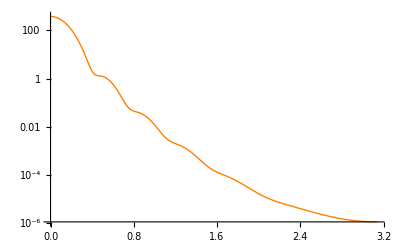

```mathematica
eik1p3=LogPlot[eik1interp3[θ],{θ,0,Pi},PlotStyle->Orange]
```

```mathematica
eik2dσdΩ[3,100]
```

{{0.,373.822},{0.01,372.674},{0.02,369.25},{0.03,363.61},{0.04,355.853},{0.05,346.113},{0.06,334.557},{0.07,321.376},{0.08,306.786},{0.09,291.018},{0.1,274.315},{0.11,256.92},{0.12,239.08},{0.13,221.032},{0.14,203.002},{0.15,185.2},{0.16,167.817},{0.17,151.02},{0.18,134.955},{0.19,119.74},{0.2,105.467},{0.21,92.2049},{0.22,79.9969},{0.23,68.8639},{0.24,58.806},{0.25,49.8051},{0.26,41.8272},{0.27,34.8252},{0.28,28.7416},{0.29,23.5109},{0.3,19.0624},{0.31,15.3223},{0.32,12.2158},{0.33,9.66895},{0.34,7.60994},{0.35,5.97056},{0.36,4.68707},{0.37,3.70083},{0.38,2.95883},{0.39,2.41382},{0.4,2.02441},{0.41,1.7549},{0.42,1.57507},{0.43,1.45978},{0.44,1.38857},{0.45,1.34521},{0.46,1.31714},{0.47,1.29505},{0.48,1.27234},{0.49,1.24466},{0.5,1.2095},{0.51,1.16577},{0.52,1.11348},{0.53,1.05339},{0.54,0.986814},{0.55,0.915356},{0.56,0.840759},{0.57,0.764762},{0.58,0.689007},{0.59,0.614966},{0.6,0.543894},{0.61,0.476808},{0.62,0.41448},{0.63,0.357442},{0.64,0.306006},{0.65,0.260284},{0.66,0.220219},{0.67,0.18561},{0.68,0.156146},{0.69,0.131434},{0.7,0.111024},{0.71,0.0944338},{0.72,0.0811716},{0.73,0.0707508},{0.74,0.062705},{0.75,0.0565989},{0.76,0.0520357},{0.77,0.0486619},{0.78,0.0461698},{0.79,0.0442981},{0.8,0.0428305},{0.81,0.0415934},{0.82,0.0404524},{0.83,0.0393082},{0.84,0.0380922},{0.85,0.036762},{0.86,0.0352969},{0.87,0.0336932},{0.88,0.0319608},{0.89,0.030119},{0.9,0.0281936},{0.91,0.026214},{0.92,0.0242109},{0.93,0.0222148},{0.94,0.0202541},{0.95,0.0183544},{0.96,0.0165376},{0.97,0.0148215},{0.98,0.0132201},{0.99,0.0117429},{1.,0.0103956},{1.01,0.00918054},{1.02,0.00809666},{1.03,0.00714029},{1.04,0.00630553},{1.05,0.00558473},{1.06,0.00496895},{1.07,0.00444841},{1.08,0.00401285},{1.09,0.0036519},{1.1,0.00335534},{1.11,0.00311336},{1.12,0.00291675},{1.13,0.002757},{1.14,0.00262646},{1.15,0.00251834},{1.16,0.00242674},{1.17,0.00234667},{1.18,0.00227398},{1.19,0.00220536},{1.2,0.00213821},{1.21,0.00207063},{1.22,0.0020013},{1.23,0.00192941},{1.24,0.00185457},{1.25,0.00177677},{1.26,0.00169624},{1.27,0.00161345},{1.28,0.00152899},{1.29,0.00144358},{1.3,0.00135794},{1.31,0.00127284},{1.32,0.00118901},{1.33,0.00110713},{1.34,0.00102781},{1.35,0.000951586},{1.36,0.000878911},{1.37,0.000810139},{1.38,0.000745534},{1.39,0.000685274},{1.4,0.00062945},{1.41,0.000578079},{1.42,0.000531109},{1.43,0.000488428},{1.44,0.000449873},{1.45,0.000415243},{1.46,0.000384303},{1.47,0.000356793},{1.48,0.000332439},{1.49,0.000310961},{1.5,0.000292072},{1.51,0.000275494},{1.52,0.000260954},{1.53,0.000248191},{1.54,0.00023696},{1.55,0.000227034},{1.56,0.000218204},{1.57,0.00021028},{1.58,0.000203095},{1.59,0.000196499},{1.6,0.000190363},{1.61,0.000184578},{1.62,0.00017905},{1.63,0.000173705},{1.64,0.000168482},{1.65,0.000163333},{1.66,0.000158225},{1.67,0.000153134},{1.68,0.000148044},{1.69,0.000142949},{1.7,0.000137848},{1.71,0.000132746},{1.72,0.000127652},{1.73,0.000122578},{1.74,0.000117538},{1.75,0.000112547},{1.76,0.000107621},{1.77,0.000102775},{1.78,0.0000980263},{1.79,0.0000933883},{1.8,0.0000888745},{1.81,0.000084497},{1.82,0.0000802663},{1.83,0.000076191},{1.84,0.0000722783},{1.85,0.0000685337},{1.86,0.0000649607},{1.87,0.0000615617},{1.88,0.0000583371},{1.89,0.0000552864},{1.9,0.0000524075},{1.91,0.0000496973},{1.92,0.0000471517},{1.93,0.0000447658},{1.94,0.0000425339},{1.95,0.0000404499},{1.96,0.0000385069},{1.97,0.000036698},{1.98,0.0000350159},{1.99,0.0000334533},{2.,0.0000320027},{2.01,0.0000306566},{2.02,0.0000294079},{2.03,0.0000282495},{2.04,0.0000271743},{2.05,0.0000261758},{2.06,0.0000252476},{2.07,0.0000243837},{2.08,0.0000235784},{2.09,0.0000228264},{2.1,0.0000221226},{2.11,0.0000214624},{2.12,0.0000208416},{2.13,0.0000202562},{2.14,0.0000197025},{2.15,0.0000191774},{2.16,0.0000186778},{2.17,0.0000182011},{2.18,0.0000177449},{2.19,0.000017307},{2.2,0.0000168856},{2.21,0.000016479},{2.22,0.0000160857},{2.23,0.0000157045},{2.24,0.0000153343},{2.25,0.0000149741},{2.26,0.0000146231},{2.27,0.0000142808},{2.28,0.0000139464},{2.29,0.0000136195},{2.3,0.0000132998},{2.31,0.0000129869},{2.32,0.0000126806},{2.33,0.0000123807},{2.34,0.000012087},{2.35,0.0000117995},{2.36,0.000011518},{2.37,0.0000112425},{2.38,0.000010973},{2.39,0.0000107094},{2.4,0.0000104517},{2.41,0.0000102},{2.42,9.9541×10^-6},{2.43,9.71413×10^-6},{2.44,9.48006×10^-6},{2.45,9.25188×10^-6},{2.46,9.02958×10^-6},{2.47,8.81313×10^-6},{2.48,8.60252×10^-6},{2.49,8.39771×10^-6},{2.5,8.19866×10^-6},{2.51,8.00534×10^-6},{2.52,7.81768×10^-6},{2.53,7.63564×10^-6},{2.54,7.45914×10^-6},{2.55,7.28812×10^-6},{2.56,7.1225×10^-6},{2.57,6.96219×10^-6},{2.58,6.80711×10^-6},{2.59,6.65716×10^-6},{2.6,6.51226×10^-6},{2.61,6.37229×10^-6},{2.62,6.23715×10^-6},{2.63,6.10675×10^-6},{2.64,5.98097×10^-6},{2.65,5.85971×10^-6},{2.66,5.74284×10^-6},{2.67,5.63027×10^-6},{2.68,5.52189×10^-6},{2.69,5.41757×10^-6},{2.7,5.31722×10^-6},{2.71,5.22072×10^-6},{2.72,5.12797×10^-6},{2.73,5.03885×10^-6},{2.74,4.95327×10^-6},{2.75,4.87111×10^-6},{2.76,4.79228×10^-6},{2.77,4.71668×10^-6},{2.78,4.64421×10^-6},{2.79,4.57479×10^-6},{2.8,4.5083×10^-6},{2.81,4.44468×10^-6},{2.82,4.38382×10^-6},{2.83,4.32566×10^-6},{2.84,4.2701×10^-6},{2.85,4.21707×10^-6},{2.86,4.16649×10^-6},{2.87,4.1183×10^-6},{2.88,4.07243×10^-6},{2.89,4.0288×10^-6},{2.9,3.98736×10^-6},{2.91,3.94804×10^-6},{2.92,3.91079×10^-6},{2.93,3.87556×10^-6},{2.94,3.84228×10^-6},{2.95,3.81092×10^-6},{2.96,3.78143×10^-6},{2.97,3.75376×10^-6},{2.98,3.72787×10^-6},{2.99,3.70372×10^-6},{3.,3.68128×10^-6},{3.01,3.66052×10^-6},{3.02,3.64139×10^-6},{3.03,3.62389×10^-6},{3.04,3.60797×10^-6},{3.05,3.59362×10^-6},{3.06,3.58081×10^-6},{3.07,3.56953×10^-6},{3.08,3.55975×10^-6},{3.09,3.55147×10^-6},{3.1,3.54466×10^-6},{3.11,3.53933×10^-6},{3.12,3.53547×10^-6},{3.13,3.53305×10^-6},{3.14,3.5321×10^-6}}

```mathematica
eik2interp3=Interpolation[%];
```

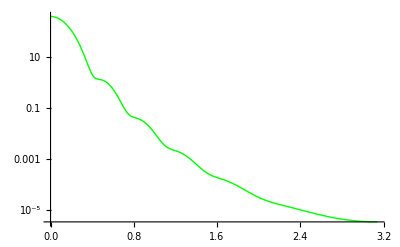

```mathematica
eik2p3=LogPlot[eik2interp3[θ],{θ,0,Pi},PlotStyle->Green]
```

```mathematica
eik3dσdΩ[3,100]
```

{{0.,373.882},{0.01,372.735},{0.02,369.312},{0.03,363.674},{0.04,355.921},{0.05,346.185},{0.06,334.632},{0.07,321.456},{0.08,306.871},{0.09,291.108},{0.1,274.408},{0.11,257.017},{0.12,239.18},{0.13,221.134},{0.14,203.105},{0.15,185.304},{0.16,167.919},{0.17,151.121},{0.18,135.053},{0.19,119.833},{0.2,105.556},{0.21,92.2879},{0.22,80.0736},{0.23,68.9337},{0.24,58.8686},{0.25,49.8603},{0.26,41.8749},{0.27,34.8655},{0.28,28.7747},{0.29,23.5372},{0.3,19.0824},{0.31,15.3365},{0.32,12.2248},{0.33,9.6733},{0.34,7.61029},{0.35,5.96753},{0.36,4.68126},{0.37,3.69283},{0.38,2.94915},{0.39,2.40294},{0.4,2.01275},{0.41,1.74283},{0.42,1.56289},{0.43,1.44773},{0.44,1.37685},{0.45,1.33395},{0.46,1.30644},{0.47,1.28496},{0.48,1.26289},{0.49,1.23585},{0.5,1.2013},{0.51,1.15816},{0.52,1.1064},{0.53,1.0468},{0.54,0.98066},{0.55,0.909591},{0.56,0.835335},{0.57,0.75964},{0.58,0.684151},{0.59,0.610346},{0.6,0.539485},{0.61,0.472591},{0.62,0.410439},{0.63,0.353565},{0.64,0.302284},{0.65,0.25671},{0.66,0.216785},{0.67,0.18231},{0.68,0.152974},{0.69,0.128381},{0.7,0.108083},{0.71,0.0915958},{0.72,0.078427},{0.73,0.0680893},{0.74,0.0601163},{0.75,0.0540727},{0.76,0.049562},{0.77,0.0462313},{0.78,0.0437742},{0.79,0.0419304},{0.8,0.0404853},{0.81,0.0392669},{0.82,0.0381424},{0.83,0.0370144},{0.84,0.035816},{0.85,0.0345062},{0.86,0.0330658},{0.87,0.0314922},{0.88,0.0297962},{0.89,0.0279978},{0.9,0.026123},{0.91,0.0242013},{0.92,0.0222633},{0.93,0.020339},{0.94,0.0184561},{0.95,0.0166393},{0.96,0.0149096},{0.97,0.0132837},{0.98,0.0117744},{0.99,0.0103901},{1.,0.00913545},{1.01,0.00801148},{1.02,0.00701622},{1.03,0.0061451},{1.04,0.00539141},{1.05,0.00474686},{1.06,0.00420201},{1.07,0.00374671},{1.08,0.0033705},{1.09,0.00306293},{1.1,0.00281383},{1.11,0.00261357},{1.12,0.00245319},{1.13,0.00232455},{1.14,0.00222041},{1.15,0.00213444},{1.16,0.00206126},{1.17,0.00199639},{1.18,0.00193622},{1.19,0.00187793},{1.2,0.00181942},{1.21,0.00175923},{1.22,0.00169647},{1.23,0.00163069},{1.24,0.00156184},{1.25,0.00149014},{1.26,0.00141608},{1.27,0.00134025},{1.28,0.0012634},{1.29,0.00118628},{1.3,0.00110967},{1.31,0.00103431},{1.32,0.000960901},{1.33,0.000890047},{1.34,0.000822281},{1.35,0.000758034},{1.36,0.000697641},{1.37,0.000641336},{1.38,0.000589264},{1.39,0.00054148},{1.4,0.000497961},{1.41,0.000458616},{1.42,0.000423296},{1.43,0.000391801},{1.44,0.000363898},{1.45,0.000339322},{1.46,0.000317791},{1.47,0.000299012},{1.48,0.000282692},{1.49,0.000268539},{1.5,0.000256272},{1.51,0.000245621},{1.52,0.000236336},{1.53,0.000228186},{1.54,0.00022096},{1.55,0.00021447},{1.56,0.000208552},{1.57,0.000203063},{1.58,0.000197881},{1.59,0.000192905},{1.6,0.000188055},{1.61,0.000183266},{1.62,0.000178491},{1.63,0.000173694},{1.64,0.000168855},{1.65,0.000163963},{1.66,0.000159015},{1.67,0.000154015},{1.68,0.000148975},{1.69,0.000143908},{1.7,0.000138832},{1.71,0.000133767},{1.72,0.000128734},{1.73,0.000123753},{1.74,0.000118844},{1.75,0.000114026},{1.76,0.000109317},{1.77,0.000104734},{1.78,0.000100289},{1.79,0.0000959952},{1.8,0.0000918617},{1.81,0.0000878961},{1.82,0.0000841038},{1.83,0.0000804882},{1.84,0.0000770507},{1.85,0.0000737911},{1.86,0.0000707075},{1.87,0.0000677969},{1.88,0.0000650548},{1.89,0.0000624759},{1.9,0.0000600539},{1.91,0.000057782},{1.92,0.0000556527},{1.93,0.0000536585},{1.94,0.0000517912},{1.95,0.0000500429},{1.96,0.0000484056},{1.97,0.0000468713},{1.98,0.0000454322},{1.99,0.000044081},{2.,0.0000428103},{2.01,0.0000416134},{2.02,0.0000404838},{2.03,0.0000394155},{2.04,0.0000384028},{2.05,0.0000374405},{2.06,0.0000365238},{2.07,0.0000356482},{2.08,0.0000348099},{2.09,0.0000340051},{2.1,0.0000332308},{2.11,0.0000324839},{2.12,0.0000317619},{2.13,0.0000310626},{2.14,0.000030384},{2.15,0.0000297244},{2.16,0.0000290822},{2.17,0.0000284563},{2.18,0.0000278456},{2.19,0.0000272491},{2.2,0.0000266661},{2.21,0.000026096},{2.22,0.0000255382},{2.23,0.0000249923},{2.24,0.0000244579},{2.25,0.0000239349},{2.26,0.000023423},{2.27,0.0000229221},{2.28,0.0000224319},{2.29,0.0000219525},{2.3,0.0000214836},{2.31,0.0000210254},{2.32,0.0000205776},{2.33,0.0000201403},{2.34,0.0000197135},{2.35,0.000019297},{2.36,0.0000188908},{2.37,0.0000184948},{2.38,0.000018109},{2.39,0.0000177334},{2.4,0.0000173677},{2.41,0.0000170119},{2.42,0.000016666},{2.43,0.0000163297},{2.44,0.0000160031},{2.45,0.0000156858},{2.46,0.0000153778},{2.47,0.0000150789},{2.48,0.0000147891},{2.49,0.000014508},{2.5,0.0000142355},{2.51,0.0000139716},{2.52,0.0000137159},{2.53,0.0000134683},{2.54,0.0000132286},{2.55,0.0000129966},{2.56,0.0000127722},{2.57,0.0000125551},{2.58,0.0000123452},{2.59,0.0000121423},{2.6,0.0000119462},{2.61,0.0000117566},{2.62,0.0000115736},{2.63,0.0000113967},{2.64,0.000011226},{2.65,0.0000110612},{2.66,0.0000109021},{2.67,0.0000107485},{2.68,0.0000106004},{2.69,0.0000104576},{2.7,0.0000103198},{2.71,0.0000101871},{2.72,0.0000100591},{2.73,9.93583×10^-6},{2.74,9.81711×10^-6},{2.75,9.7028×10^-6},{2.76,9.59278×10^-6},{2.77,9.48693×10^-6},{2.78,9.38514×10^-6},{2.79,9.2873×10^-6},{2.8,9.19329×10^-6},{2.81,9.10302×10^-6},{2.82,9.01638×10^-6},{2.83,8.93329×10^-6},{2.84,8.85365×10^-6},{2.85,8.77737×10^-6},{2.86,8.70438×10^-6},{2.87,8.63459×10^-6},{2.88,8.56793×10^-6},{2.89,8.50432×10^-6},{2.9,8.44371×10^-6},{2.91,8.38602×10^-6},{2.92,8.33119×10^-6},{2.93,8.27917×10^-6},{2.94,8.22989×10^-6},{2.95,8.18332×10^-6},{2.96,8.1394×10^-6},{2.97,8.09808×10^-6},{2.98,8.05933×10^-6},{2.99,8.02309×10^-6},{3.,7.98935×10^-6},{3.01,7.95805×10^-6},{3.02,7.92917×10^-6},{3.03,7.90268×10^-6},{3.04,7.87855×10^-6},{3.05,7.85676×10^-6},{3.06,7.83728×10^-6},{3.07,7.8201×10^-6},{3.08,7.8052×10^-6},{3.09,7.79256×10^-6},{3.1,7.78217×10^-6},{3.11,7.77403×10^-6},{3.12,7.76811×10^-6},{3.13,7.76442×10^-6},{3.14,7.76296×10^-6}}

```mathematica
eik3interp3=Interpolation[%];
```

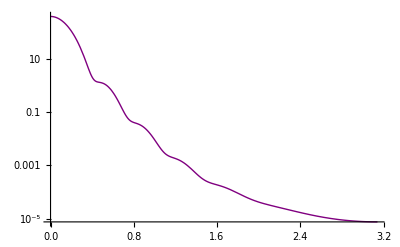

```mathematica
eik3p3=LogPlot[eik3interp3[θ],{θ,0,Pi},PlotStyle->Purple]
```

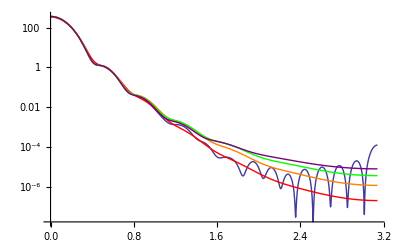

```mathematica
Show[p3,eik0p3,eik1p3,eik2p3,eik3p3,PlotRange->Automatic]
```

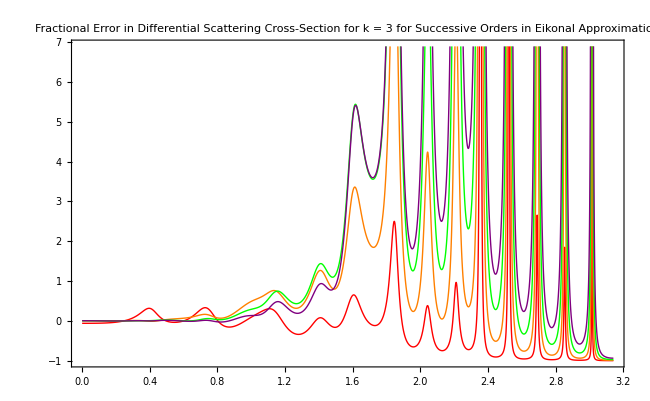

```mathematica
Plot[{(eik0interp3[θ]-temp[θ])/temp[θ],(eik1interp3[θ]-temp[θ])/temp[θ],(eik2interp3[θ]-temp[θ])/temp[θ],(eik3interp3[θ]-temp[θ])/temp[θ]},{θ,0,Pi},PlotLabel->"Fractional Error in Differential Scattering Cross-Section
for k = 3 for Successive Orders in Eikonal Approximation",PlotStyle->{Red,Orange,Green,Purple},PlotLegend->{"Zeroth Order Eikonal","First Order Eikonal","Second Order Eikonal","Third Order Eikonal"},AxesLabel->{θ},LegendPosition->{.85,-0.2},LegendSize->{.9,0.4},ImageSize->650,Frame->True]
```

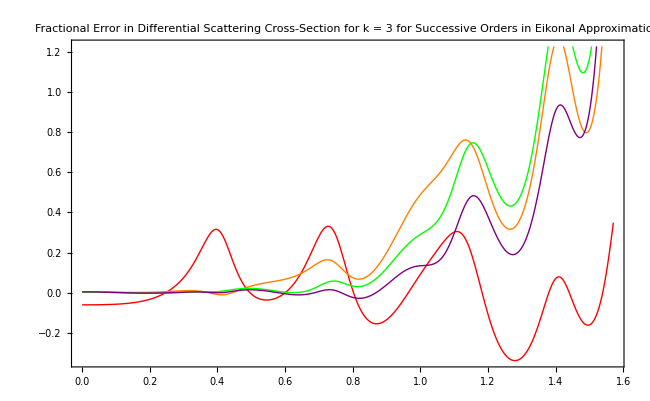

```mathematica
Plot[{(eik0interp3[θ]-temp[θ])/temp[θ],(eik1interp3[θ]-temp[θ])/temp[θ],(eik2interp3[θ]-temp[θ])/temp[θ],(eik3interp3[θ]-temp[θ])/temp[θ]},{θ,0,Pi/2},PlotLabel->"Fractional Error in Differential Scattering Cross-Section
for k = 3 for Successive Orders in Eikonal Approximation",AxesLabel->{θ},PlotStyle->{Red,Orange,Green,Purple},PlotLegend->{"Zeroth Order Eikonal","First Order Eikonal","Second Order Eikonal","Third Order Eikonal"},LegendPosition->{.85,-0.2},LegendSize->{.9,0.4},ImageSize->650,Frame->True]
```

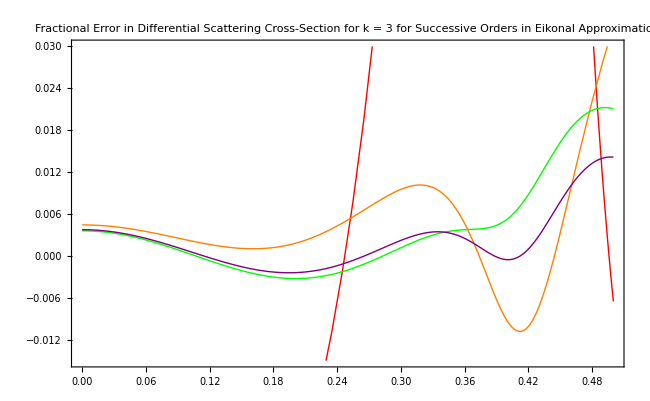

```mathematica
Plot[{(eik0interp3[θ]-temp[θ])/temp[θ],(eik1interp3[θ]-temp[θ])/temp[θ],(eik2interp3[θ]-temp[θ])/temp[θ],(eik3interp3[θ]-temp[θ])/temp[θ]},{θ,0,.5},PlotRange->{-.015,.03},PlotLabel->"Fractional Error in Differential Scattering Cross-Section
for k = 3 for Successive Orders in Eikonal Approximation",AxesLabel->{θ},PlotStyle->{Red,Orange,Green,Purple},PlotLegend->{"Zeroth Order Eikonal","First Order Eikonal","Second Order Eikonal","Third Order Eikonal"},LegendPosition->{.85,-0.2},LegendSize->{.9,0.4},ImageSize->650,Frame->True]
```

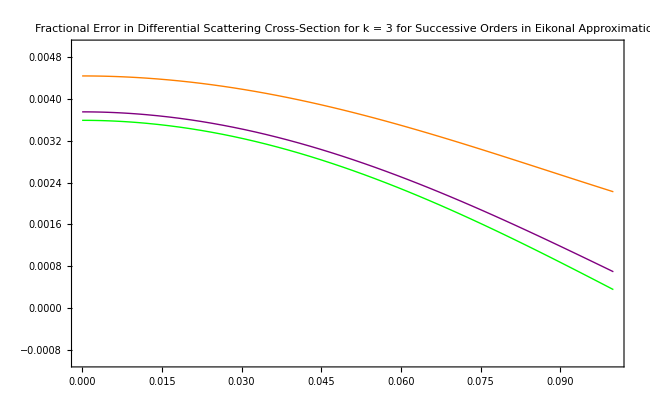

```mathematica
Plot[{(eik0interp3[θ]-temp[θ])/temp[θ],(eik1interp3[θ]-temp[θ])/temp[θ],(eik2interp3[θ]-temp[θ])/temp[θ],(eik3interp3[θ]-temp[θ])/temp[θ]},{θ,0,.1},PlotRange->{-0.001,0.005},PlotLabel->"Fractional Error in Differential Scattering Cross-Section
for k = 3 for Successive Orders in Eikonal Approximation",AxesLabel->{θ},PlotStyle->{Red,Orange,Green,Purple},PlotLegend->{"Zeroth Order Eikonal","First Order Eikonal","Second Order Eikonal","Third Order Eikonal"},LegendPosition->{.85,-0.2},LegendSize->{.9,0.4},ImageSize->650,Frame->True]
```

As can be seen from the above four graphs, the fractional error in general becomes smaller as we go to higher orders in the eikonal series. Furthermore, the range of validity in θ increases with increasing order. The only exception to these results can be seen upon close inspection of the forward scattering direction. In the forward direction, the approximation to second order actually has a smaller fractional error than the approximation to third order.

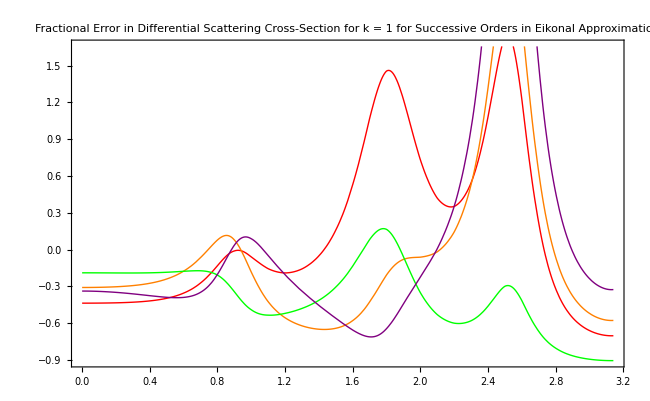

```mathematica
Plot[{(eik0interp1[θ]-interp1[θ])/interp1[θ],(eik1interp1[θ]-interp1[θ])/interp1[θ],(eik2interp1[θ]-interp1[θ])/interp1[θ],(eik3interp1[θ]-interp1[θ])/interp1[θ]},{θ,0,Pi},PlotLabel->"Fractional Error in Differential Scattering Cross-Section
for k = 1 for Successive Orders in Eikonal Approximation",PlotStyle->{Red,Orange,Green,Purple},PlotLegend->{"Zeroth Order Eikonal","First Order Eikonal","Second Order Eikonal","Third Order Eikonal"},AxesLabel->{θ},LegendPosition->{.85,-0.2},LegendSize->{.9,0.4},ImageSize->650,Frame->True]
```